## Initialization

#### Requires custom libraries (‘GRindices’, ‘GRtensors’ and ‘tensor’) from S. Gubser to be in the same directory as the notebook

```mathematica
SetDirectory[NotebookDirectory[]];
<<GRtensors
```

#### Define the metric tensor for a conformal geometry with a horizon

```mathematica
ggValues={{-f[z]y[z],0,0,0},{0,y[z],0,0},{0,0,y[z],0},{0,0,0,y[z]/f[z]}};
ggiValues=Inverse[ggValues];
SetXMet[{t,x1,x2,z},ggValues,ggiValues];
NewTensor[chris,chrisDef,Simplify]
DisplayTensor[gg]//MatrixForm
```

gg[{DownVector,DownVector}] has components

(-f[z] y[z] | 0 | 0 | 0
0 | y[z] | 0 | 0
0 | 0 | y[z] | 0
0 | 0 | 0 | y[z]/f[z])

#### For AdS5-Schwarzschild we need

```mathematica
AdSSchRules={y->Function[z,1/z^2],f->Function[z,1-z^4]};
```

#### Range for the upper and lower indices on the worldsheet (WS)

```mathematica
range[DownWS]={1,2};
range[UpWS]={1,2};
```

#### Define the WS coordinates σ^a

```mathematica
σaValues={τ,σ};
σaDef[DefaultIndexType]={UpWS};
σaDef[{a_}]:=σaValues[[a]];
NewTensor[σa,σaDef];
```

#### Define the embedding functions X^μ in a generic (τ, σ) gauge

```mathematica
XμValues={t[τ,σ],x1[τ,σ],x2[τ,σ],z[τ,σ]};
XμDef[DefaultIndexType]={UpVector};
XμDef[{m_}]:=XμValues[[m]];
NewTensor[Xμ,XμDef]
```

#### Define ∂_a X^μ

```mathematica
dXDef[DefaultIndexType]={DownWS,UpVector};
dXDef[{a_,m_}]:=D[Xμ[{m}],σa[{a}]];
NewTensor[dX,dXDef];
```

#### Define the worldsheet metric in a generalized conformal gauge (in terms of a ‘stretching function’)

```mathematica
habValues={{-s[τ,σ],0},{0,1/s[τ,σ]}};
habDef[DefaultIndexType]={DownWS,DownWS};
habDef[{a_,b_}]:=habValues[[a,b]];
NewTensor[hab,habDef,Simplify]
```

#### The determinant and the inverse of the WS metric

```mathematica
deth=Simplify[Det[DisplayTensor[hab]]];
habInverseValues=Simplify[Inverse[DisplayTensor[hab]]];
```

hab[{DownWS,DownWS}] has components

hab[{DownWS,DownWS}] has components

#### Define the worldsheet currents (Π^a)_μ

```mathematica
ΠμaValues=Simplify[-τf habInverseValues . DisplayTensor[dX] . (DisplayTensor[gg]/.z->z[τ,σ])];
ΠμaDef[DefaultIndexType]={DownVector,UpWS};
ΠμaDef[{m_,a_}]:=ΠμaValues[[a,m]];
NewTensor[Πμa,ΠμaDef];
```

dX[{DownWS,UpVector}] has components

gg[{DownVector,DownVector}] has components

#### Equations of motion

```mathematica
ΠeomDef[DefaultIndexType]={DownVector};
ΠeomDef[{m_}]:=Sum[D[√-deth Πμa[{m,a}],σa[{a}]],{a,1,2}]-√-deth Sum[(chris[{m,k,l}]/.z->z[τ,σ])dX[{a,l}]Πμa[{k,a}],{k,1,dim},{l,1,dim},{a,1,2}];
NewTensor[Πeom,ΠeomDef,Simplify]
```

#### Induced worldsheet metric

```mathematica
γabDef[DefaultIndexType]={DownWS,DownWS};
γabDef[{a_,b_}]:=Sum[(gg[{μ,ν}]/.z->z[τ,σ])dX[{a,μ}]dX[b,ν],{μ,1,dim},{ν,1,dim}];
NewTensor[γab,γabDef,Simplify]
```

#### Constraint equations

```mathematica
ConstraintsDef[DefaultIndexType]={DownWS,DownWS};
ConstraintsDef[{a_,b_}]:=γab[{a,b}]-1/2 hab[{a,b}]Sum[habInverseValues[[c,d]]γab[{c,d}],{c,1,2},{d,1,2}];
NewTensor[Constraints,ConstraintsDef,Simplify]
```

## Initial and boundary conditions

#### Particular stretching function we will use

```mathematica
StretchingRule={s->Function[{τ,σ},(1-z[τ,σ])/(1-z0)z0^2/z[τ,σ]^2]};
```

#### Choose the initial profile of the string

```mathematica
ICPosRules={t[0,σ]->0,x1[0,σ]->0,x2[0,σ]->0,z[0,σ]->z0};
```

#### Boundary conditions for free string endpoints

```mathematica
BCRules={
Derivative[0,1][t][τ,0]->0,Derivative[0,1][t][τ,π]->0,
Derivative[0,1][x1][τ,0]->0,Derivative[0,1][x1][τ,π]->0,
Derivative[0,1][x2][τ,0]->0,Derivative[0,1][x2][τ,π]->0,
Derivative[0,1][z][τ,0]->0,Derivative[0,1][z][τ,π]->0
};
```

#### Choosing the pointlike initial conditions automatically satisfies one of the constraint equations:

```mathematica
Constraints[{2,1}]/.τ->0/.ICPosRules/.Derivative[0,1][t][0,σ]->(D[t[0,σ]/.ICPosRules,σ])/.Derivative[0,1][x1][0,σ]->(D[x1[0,σ]/.ICPosRules,σ])/.Derivative[0,1][x2][0,σ]->(D[x2[0,σ]/.ICPosRules,σ])/.Derivative[0,1][z][0,σ]->(D[z[0,σ]/.ICPosRules,σ])//Simplify
```

0

#### Choose the velocity profile in the y-direction that satisfies the following: (a) Sends one of the endpoints in one direction, and creates a kink in the part of the string close to it in the opposite direction (b) Integrates to zero (c) Is consistent with the boundary conditions

#### Choose Gaussians

```mathematica
G[x_,μ_,σ_]:=Exp[-1/2 ((x-μ)/σ)^2]/(σ √(2 π));
DG[x_,μ_,σ_]=D[G[x,μ,σ],x];
```

#### Look for solution in the form G[x,0,0.1]-G[x,0.3,0.1] to satisfy (a), but then in order to satisfy (b) and (c), introduce two unknowns in the form A*G[x-F,0,0.1]-G[x-F,0.3,0.1]

#### Create a list of F’s that will satisfy the b.c. at x=0

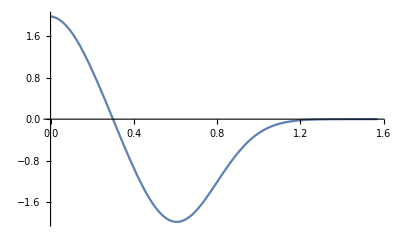

```mathematica
μ1=0;σ1=0.2;
μ2=0.6;σ2=0.2;
Plot[G[x,μ1,σ1]-G[x,μ2,σ2],{x,0,π/2},PlotRange->All]
```

```mathematica
FSolList={};
Do[
FSol=F/.FindRoot[A*DG[0-F,μ1,σ1]-DG[0-F,μ2,σ2]==0,{F,0}];
FSolList=Append[FSolList,{A,FSol}];
,{A,1,3,0.01}];
FInt=Interpolation[FSolList];
```

#### Compute the integral of the velocity profile for those F’s as a functions of A

```mathematica
ASolList=Table[{A,NIntegrate[A*G[x-FInt[A],μ1,σ1]-G[x-FInt[A],μ2,σ2],{x,0,π}]},{A,1,3,0.01}];
AInt=Interpolation[ASolList];
```

#### Find the optimum A and F, and use them to define the velocity profile

```mathematica
AOpt=A/.FindRoot[AInt[A]==0,{A,2}];
FOpt=FInt[AOpt];
yVelProf[x_]=B*(AOpt*G[x-FOpt,μ1,σ1]-G[x-FOpt,μ2,σ2]);
```

#### Check that it satisfies the (a), (b) and (c) criteria

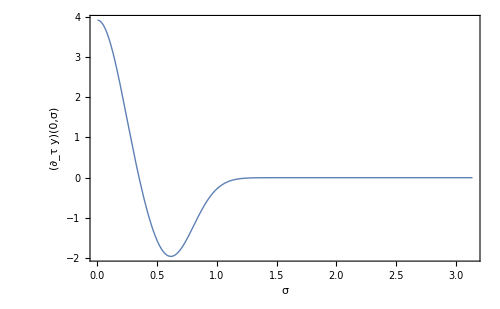

```mathematica
yVelPlot=Plot[yVelProf[x]/.B->1,{x,0,π},PlotRange->All,PlotStyle->Thick,Axes->False,Frame->True,FrameLabel->{Style["σ",FontSize->15,Italic,Bold],Style["(∂_τ y)(0,σ)",FontSize->15,Italic,Bold]},LabelStyle->{Directive[Black,12],FontFamily->"Helvetica"},RotateLabel->True,ImageSize->500]
```

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["yVelPlot.pdf",yVelPlot];
```

```mathematica
{D[yVelProf[x],x]/.x->0,D[yVelProf[x],x]/.x->π,NIntegrate[yVelProf[x]/.B->2,{x,0,π}]}/.B->2
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {5.6345×10^-8}. NIntegrate obtained -5.0554×10^-12 and 4.66849×10^-12 for the integral and error estimates.

{-1.2673×10^-10,2.66111×10^-33,-5.0554×10^-12}

#### Choose the other two spatial initial velocity profiles consistent with the boundary conditions

```mathematica
ICVelRules={
Derivative[1,0][x1][0,σ]->z0*A*Cos[σ],
Derivative[1,0][x2][0,σ]->yVelProf[σ],
Derivative[1,0][z][0,σ]->z0*√f[z0]*(1-Cos[2σ])/.AdSSchRules
};
```

#### Finally, the initial t-velocity we get from the other constraint equation

```mathematica
tpRule=Assuming[z0>0&&z0<1,Simplify[(Solve[(Constraints[{1,1}]/.τ->0/.ICPosRules/.Derivative[0,1][t][0,σ]->(D[t[0,σ]/.ICPosRules,σ])/.Derivative[0,1][x1][0,σ]->(D[x1[0,σ]/.ICPosRules,σ])/.Derivative[0,1][x2][0,σ]->(D[x2[0,σ]/.ICPosRules,σ])/.Derivative[0,1][z][0,σ]->(D[z[0,σ]/.ICPosRules,σ])//Simplify)==0,Derivative[1,0][t][0,σ]]//Simplify)[[2]]/.AdSSchRules/.ICVelRules]]
```

{t^(1,0)[0,σ]→-(√((1-z0^4) (B^2 (1.99471 ⅇ^(-12.5 (-0.603237+σ)^2)-3.93352 ⅇ^(-12.5 (-0.00323723+σ)^2))^2+A^2 z0^2 Cos[σ]^2+4 z0^2 Sin[σ]^4)))/(-1+z0^4)}

#### Check one more time that the constraint equations are satisfied

```mathematica
ICBCRules=Join[ICPosRules,BCRules,ICVelRules,tpRule];
```

```mathematica
Table[Constraints[{a,b}],{a,1,2},{b,1,2}]/.τ->0/.ICBCRules/.Derivative[0,1][t][0,σ]->(D[t[0,σ]/.ICBCRules,σ])/.Derivative[0,1][x1][0,σ]->(D[x1[0,σ]/.ICBCRules,σ])/.Derivative[0,1][x2][0,σ]->(D[x2[0,σ]/.ICBCRules,σ])/.Derivative[0,1][z][0,σ]->(D[z[0,σ]/.ICBCRules,σ])/.AdSSchRules//Simplify
```

{{0.,0},{0,0.}}

#### Prepare for use in NDSolve

```mathematica
ICBC=Join[Table[ICBCRules[[i,1]]==ICBCRules[[i,2]],{i,1,Length[ICBCRules]}]];
```

## Solving string EoMs

#### Define equations of motion with all the bells and whistles included and solve them

```mathematica
EoMs={Πeom[{1}],Πeom[{2}],Πeom[{3}],Πeom[{4}]}/.StretchingRule/.AdSSchRules/.τf->1//Simplify;
```

#### Choose initial values

```mathematica
InitialValues={z0->0.1,A->4000,B->30,τMax->8};
```

#### Solve

```mathematica
Sol=NDSolve[{Table[EoMs[[i]]==0,{i,1,dim}],ICBC}/.InitialValues,{t,x1,x2,z},{τ,0,τMax/.InitialValues},{σ,0,π},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->1200}}][[1]];
τM=Sol[[1,2,1,1,2]];
tsol[τ_,σ_]:=t[τ,σ]/.Sol
xsol[τ_,σ_]:=x1[τ,σ]/.Sol
ysol[τ_,σ_]:=x2[τ,σ]/.Sol
zsol[τ_,σ_]:=z[τ,σ]/.Sol
xMax=Max[1.1xsol[0.99τM,0],Abs[1.1xsol[0.99τM,π]]];
```

NDSolve::ndsz: At τ == 0.0694322, step size is effectively zero; singularity or stiff system suspected.

NDSolve::eerr: Warning: scaled local spatial error estimate of 353.134 at τ = 0.0694322 in the direction of independent variable σ is much greater than the prescribed error tolerance. Grid spacing with 1201 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

#### Define how may steps in τ, t and σ we will use in plotting

```mathematica
τNum=30;
tNum=40;
σNum=50;
```

#### Plot string shapes in the original gauge at different τ

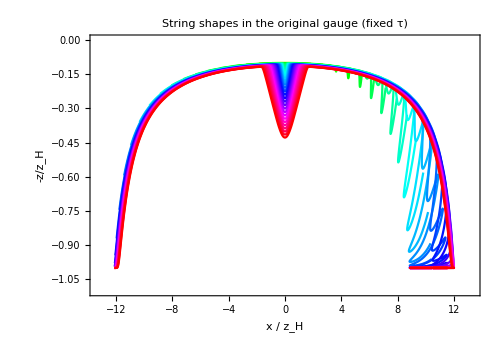

```mathematica
ParametricPlot[Evaluate[Table[{xsol[τ,σ],-zsol[τ,σ]},{τ,0,τM,τM/τNum}]],{σ,0,π},ImageSize->500,PlotRange->{{-xMax,xMax},{-1.1,0}},AspectRatio->.7,Axes->False,Frame->True,PlotStyle->Table[Hue[0.2+0.8i/τNum],{i,0,τNum}],FrameLabel->{Style["x / z_H",FontSize->15,Italic,Bold],Style["-z/z_H",FontSize->15,Italic,Bold]},LabelStyle->{Directive[Black,12],FontFamily->"Helvetica"},RotateLabel->False,PlotLabel->Style["String shapes in the original gauge (fixed τ)",FontSize->13,Bold]]
```

## Transform to static gauge

#### We need to invert the function t[τ, σ] -> τ[t, σ], which we will not be able to do for all σ (because the numerics crash), so we need to find up to what time t we can invert this for every σ (this is tTrans) and up to what maximal t (tMax) we will keep inverting

```mathematica
tTrans=tsol[τM,π/2];
tMax=0.9tsol[τM,0];
Do[tInt[n]=tMax n/tNum;,{n,1,tNum,1}];
Manipulate[
{ContourPlot[tsol[τ,σ]==tInt[n],{σ,0,π},{τ,0,τM},ImageSize->200],
Quiet[FindRoot[tsol[τM,σ1]==tInt[n],{σ1,π/2-0.1,0,π/2}]]}
,{n,1,tNum,1}]
```

#### For t>tTrans, we cannot invert for all σ, so find limits to which σ we can invert (now two classes of solutions, due to asymmetry)

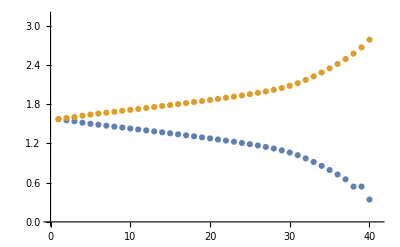

```mathematica
Do[
tInt[n]=tMax n/tNum;
If[tInt[n]<tTrans,σLimit0[n]=π/2,σLimit0[n]=σ1/.Quiet[FindRoot[tsol[τM,σ1]==tInt[n],{σ1,π/2-0.1,0,π/2}]]];
If[tInt[n]<tTrans,σLimitπ[n]=π/2,σLimitπ[n]=σ1/.Quiet[FindRoot[tsol[τM,σ1]==tInt[n],{σ1,π/2+0.1,π/2,π}]]];
,{n,1,tNum,1}]
ListPlot[{Table[{n,σLimit0[n]},{n,1,tNum,1}],Table[{n,σLimitπ[n]},{n,1,tNum,1}]},PlotRange->{{0,tNum+1},{0,π}},AxesOrigin->{0,0}]
```

#### Finally do the inversion (get rid of first tRem time instances)

```mathematica
σNumNew=100;
ProgressIndicator[Dynamic[m],{0,σNumNew}]
Do[
σLocal=m*(π/2)/σNumNew;
tsolInt[m]=Interpolation[Table[{τ,tsol[τ,σLocal]},{τ,0,τM,τM/1000}]];
,{m,0,σNumNew}]
```

```mathematica
ProgressIndicator[Dynamic[n],{1,tNum}]
Do[
τTempList0={};
Do[
σLocal=m*(π/2)/σNumNew;
If [σLocal>σLimit0[n],Break[]];
τTempList0=Append[τTempList0,{σLocal,τ/.FindRoot[tsolInt[m][τ]==tInt[n],{τ,0.5τM,0,τM}]}];
,{m,0,σNumNew}];
τStatic0[n]=Interpolation[τTempList0];
,{n,1,tNum,1}]
```

FindRoot::reged: The point {0.0694322} is at the edge of the search region {0., 0.0694322} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot :: reged will be suppressed during this calculation.

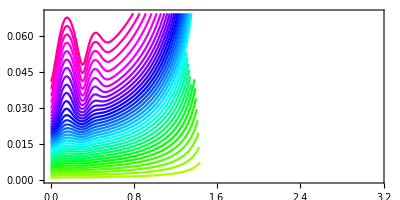

```mathematica
tRem=5;
Show[
Evaluate[Table[Plot[τStatic0[n][σ],{σ,0,σLimit0[n]},PlotStyle->Hue[0.2+0.8n/tNum]],{n,1,tNum-tRem,1}]],
ImageSize->400,PlotRange->{{0,π},{0,τM}},AspectRatio->.5,Axes->False,Frame->True]
```

#### Plot the string shapes in the static gauge (embedding functions are worldsheet scalars), i.e. for fixed times t

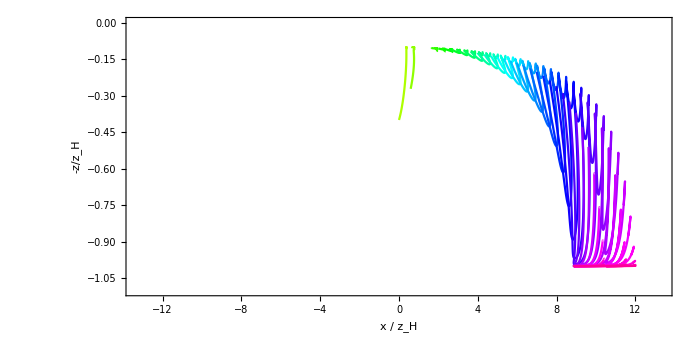

```mathematica
XZPlot=Show[
Evaluate[
Table[
ParametricPlot[{xsol[τStatic0[n][σ],σ],-zsol[τStatic0[n][σ],σ]},{σ,0,σLimit0[n]},PlotStyle->Hue[0.2+0.8n/tNum]],{n,1,tNum-tRem,1}]],
ImageSize->700,PlotRange->{{-xMax,xMax},{-1.1,0}},AspectRatio->.5,Axes->False,Frame->True,FrameLabel->{Style["x / z_H",FontSize->15,Italic,Bold],Style["-z/z_H",FontSize->15,Italic,Bold]},LabelStyle->{Directive[Black,12],FontFamily->"Helvetica"},RotateLabel->False]
```

#### Find the max value of y for plotting

```mathematica
MaxVal=Abs[ysol[τStatic0[1][0],0]];
Quiet[Do[Do[
σLocal0=i*(σLimit0[nTemp]/100);
yLocal0=Abs[ysol[τStatic0[nTemp][σLocal0],σLocal0]];
If[yLocal0>MaxVal,{MaxVal=yLocal0;LocTemp=σLocal0;nHold=nTemp;}];
(*σLocalπ=σLimitπ[nTemp]+i*((π-σLimit0[nTemp])/110);
yLocalπ=Abs[ysol[τStaticπ[nTemp][σLocalπ],σLocalπ]];
If[yLocalπ>MaxVal,MaxVal=yLocalπ;];*)
,{i,1,100,1}];,{nTemp,1,tNum-tRem,1}]]
yMax=1.1*MaxVal
```

5.43289×10^15

```mathematica
yMax=6.7
```

6.7

#### Plot in the X-Y plane

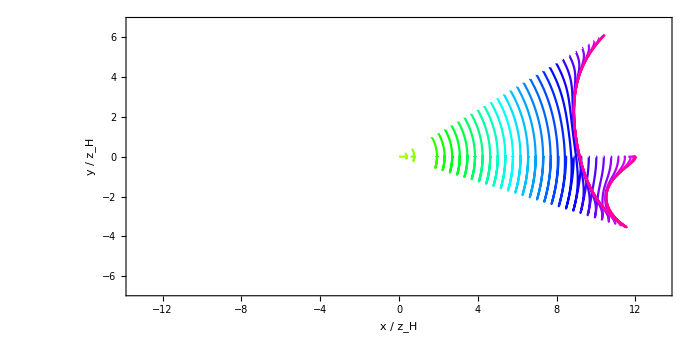

```mathematica
XYPlot=Show[
Evaluate[
Table[
ParametricPlot[{xsol[τStatic0[n][σ],σ],ysol[τStatic0[n][σ],σ]},{σ,0,σLimit0[n]},PlotStyle->Hue[0.2+0.8n/tNum]],{n,1,tNum-tRem,1}]],
ImageSize->700,PlotRange->{{-xMax,xMax},{-yMax,yMax}},AspectRatio->.5,Axes->False,Frame->True,FrameLabel->{Style["x / z_H",FontSize->15,Italic,Bold],Style["y / z_H",FontSize->15,Italic,Bold]},LabelStyle->{Directive[Black,12],FontFamily->"Helvetica"},RotateLabel->True]
```

#### Isolate the envelope in the X-Y plot (i.e. the max and min in Y and X coordinates at every time-step)

```mathematica
ProgressIndicator[Dynamic[nTemp],{1,tNum-tRem}]
MaxNum=1000;
MaxList={};MinList={};MinLocList={};
Do[
MaxVal=ysol[τStatic0[nTemp][0],0];MaxLoc=0;
MinVal=ysol[τStatic0[nTemp][0],0];MinLoc=0;
Do[
σLocal=i*(σLimit0[nTemp]/MaxNum);
yLocal=ysol[τStatic0[nTemp][σLocal],σLocal];
If[yLocal>MaxVal,{MaxVal=yLocal;MaxLoc=σLocal;}];
If[yLocal<MinVal,{MinVal=yLocal;MinLoc=σLocal;}];
,{i,1,MaxNum,1}];
MaxList=Append[MaxList,{xsol[τStatic0[nTemp][MaxLoc],MaxLoc],MaxVal}];
MinList=Append[MinList,{xsol[τStatic0[nTemp][MinLoc],MinLoc],MinVal}];
MinLocList=Append[MinLocList,{nTemp,MinLoc}];
,{nTemp,1,tNum-tRem,1}]
```

#### Location of the initial kink and the zero in the velocity profile, and the list of x-y coordinates of it at later times

```mathematica
σLocKink=x/.FindMinimum[yVelProf[x]/.InitialValues,{x,0.4}][[2]];
σLocZero=x/.FindRoot[(yVelProf[x]/.InitialValues)==0,{x,0.2}];
InitZeroList=Table[{xsol[τStatic0[n][σLocZero],σLocZero],ysol[τStatic0[n][σLocZero],σLocZero]},{n,1,tNum-tRem,1}];
InitKinkList=Table[{xsol[τStatic0[n][σLocKink],σLocKink],ysol[τStatic0[n][σLocKink],σLocKink]},{n,1,tNum-tRem,1}];
EndpointList=Table[{xsol[τStatic0[n][0],0],ysol[τStatic0[n][0],0]},{n,1,tNum-tRem,1}];
yVelPlotMod=Plot[yVelProf[x]/.B->1,{x,0,π/2},PlotRange->All,PlotStyle->Thick,Axes->False,Frame->True,FrameLabel->{Style["",FontSize->15,Italic,Bold],Style["(∂_τ y)(0,σ)",FontSize->15,Italic,Bold]},LabelStyle->{Directive[Black,12],FontFamily->"Helvetica"},RotateLabel->True,ImageSize->230];
```

#### Null geodesic stopping distance

```mathematica
ΔxGeo[zs_]:=1/zs*(√π*Gamma[5/4])/Gamma[3/4]-Hypergeometric2F1[1/4,1/2,5/4,zs^4];
```

#### Finally, plot all this together

```mathematica
XYPlot=Show[
Evaluate[Table[
ParametricPlot[{xsol[τStatic0[n][σ],σ],ysol[τStatic0[n][σ],σ]},{σ,0,σLimit0[n]},PlotStyle->Hue[0.2+0.8n/tNum],Epilog->Inset[yVelPlotMod,{-xMax/2*1.2,-yMax/2*1.2}]],{n,1,tNum-tRem,1}]],
ListPlot[{MaxList,MinList,InitKinkList,EndpointList,InitZeroList},PlotStyle->PointSize[0.007]],
Graphics[Text[Style["max y",14,Italic,Bold,ColorData[1,1],FontFamily->"Helvetica"],{-0.95xMax,0.9yMax},{-1,0}]],
Graphics[Text[Style["min y",14,Italic,Bold,ColorData[1,2],FontFamily->"Helvetica"],{-0.95xMax,0.8yMax},{-1,0}]],
Graphics[Text[Style["init. kink",14,Italic,Bold,ColorData[1,3],FontFamily->"Helvetica"],{-0.95xMax,0.7yMax},{-1,0}]],
Graphics[Text[Style["endpoint",14,Italic,Bold,ColorData[1,4],FontFamily->"Helvetica"],{-0.95xMax,0.6yMax},{-1,0}]],
Graphics[Text[Style["init. zero",14,Italic,Bold,ColorData[1,5],FontFamily->"Helvetica"],{-0.95xMax,0.5yMax},{-1,0}]],
Graphics[Text[Style["null geo. (dashed)",14,Italic,Black,FontFamily->"Helvetica"],{-0.95xMax,0.4yMax},{-1,0}]],
Graphics[Text[Style["A = "<>ToString[A/.InitialValues],16,Italic,Bold,Black,FontFamily->"Helvetica"],{-0.6xMax,0.9yMax},{-1,0}]],
Graphics[Text[Style["B = "<>ToString[B/.InitialValues],16,Italic,Bold,Black,FontFamily->"Helvetica"],{-0.6xMax,0.75yMax},{-1,0}]],
Graphics[{Dashed,Black,Circle[{0,0},ΔxGeo[z0]/.InitialValues,{-π/2,π/2}]}],
ImageSize->700,PlotRange->{{-xMax,xMax},{-yMax,yMax}},AspectRatio->.5,Axes->False,Frame->True,FrameLabel->{Style["x / z_H",FontSize->15,Italic,Bold],Style["y / z_H",FontSize->15,Italic,Bold]},LabelStyle->{Directive[Black,12],FontFamily->"Helvetica"},RotateLabel->True]
```

-Graphics-

```mathematica
(*Export["XYPlotNew.pdf",XYPlot];
```

## Stopping distances analytically

### PDE for velocity in AdS and matching to AdS-Schwarzschild

#### Note that first, for comparison, we have to be a bit careful about have we defined the angle: θExact(σ) is in fact a Tan of the actual angle -- this turns out to be important in comparisons

```mathematica
θMExact[σ_]=ArcTan[θExact[σ]];
θMaxME=θMExact[0];
θMinME=θMExact[σLocKink];
P0tInitME[σ_]:=-P0τInit[σ]/θMExact'[σ];
P0tInitTME=Interpolation[Table[{θMExact[σ],P0tInitME[σ]},{σ,0,σLocKink,σLocKink/1000}]];
```

#### EoM (tested in a separate notebook in AdS) is

```mathematica
vEoM=Derivative[2,0][ζ][t,θ]-2/P0tInitTME[θ]^2*(t^2-ζ[t,θ]^2+(Derivative[0,1][ζ][t,θ])^2)/((z0/.InitialValues)+ζ[t,θ])^5;
```

#### Initial and boundary conditions are approximately

```mathematica
vICBC={ζ[0,θ]==0,Derivative[1,0][ζ][0,θ]==0,ζ[t,θMinME]==0,ζ[t,θMaxME]==0};
```

#### Solve it

```mathematica
vSol=NDSolve[Join[{vEoM==0},vICBC],ζ,{t,0,1000},{θ,θMinME,θMaxME}][[1]];
```

#### String solution in AdS is then given by

```mathematica
rString[t_,θ_]=√(t^2-ζ[t,θ]^2)/.vSol;
zString[t_,θ_]=z0+ζ[t,θ]/.vSol/.InitialValues;
```

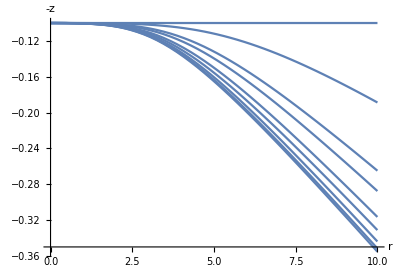

```mathematica
ParametricPlot[Table[{rString[t,θ],-zString[t,θ]},{θ,θMinME,θMaxME,0.1}],{t,0,10},PlotRange->All,AspectRatio->0.7,AxesLabel->{"r","-z"}]
```

#### Now let’s try to match this to AdS-Schwarzschild case by equating p_z / E at some time t_*

```mathematica
Clear[χzS4];
pzEAdSSch=1/f[z]*√(1-f[z]/R^2)/.R->√(1-χzS4);
pzEAdS=Derivative[1,0][ζ][t,θ]/.t->tS;
χzS4Rule=Solve[pzEAdSSch==pzEAdS,χzS4][[1]]
```

{χzS4→(-1+f[z]+f[z]^2 (ζ^(1,0)[tS,θ])^2)/(-1+f[z]^2 (ζ^(1,0)[tS,θ])^2)}

#### From the previous section, we know that AdS-Sch geodesics are given by

```mathematica
rGeo[z_]=-1/z Hypergeometric2F1[1/4,1/2,5/4,χzS4/z^4];
```

#### The final distribution of stopping distances is then given by

```mathematica
rFinalStop[tS_,θ_]=(rString[tS,θ]+rGeo[1]-rGeo[z])/.χzS4Rule/.AdSSchRules/.z->zString[tS,θ]/.vSol;
```

#### Compare with the numerical results

```mathematica
rStopNum=Interpolation[Table[{θExact[σ],√(xsol[τM,σ]^2+ysol[τM,σ]^2)},{σ,0,σLocKink,σLocKink/1000}]];
```

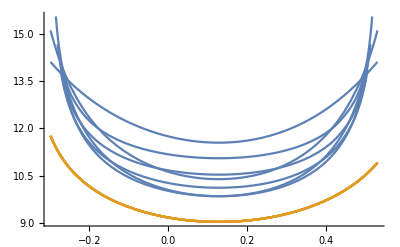

```mathematica
Show[Table[Plot[{rFinalStop[tS,θ],rStopNum[θ]},{θ,θMinME,θMaxME}],{tS,2,8,1}],AxesOrigin->{0,0},PlotRange->All]
```

#### Doesn’t really seem to work, let’s inspect the trajectories

#### First, make sure the angles I assume are the actual angles

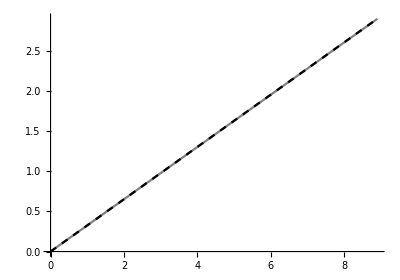

```mathematica
σLocal=0.1;
ParametricPlot[{{xsol[τ,σLocal],ysol[τ,σLocal]},{xsol[τ,σLocal],xsol[τ,σLocal]Tan[θMExact[σLocal]]}},{τ,0,0.99τM},AspectRatio->0.7,PlotStyle->{{Gray},{Black,Dashed}},PlotRange->All]
```

#### Good. Let’s look at some σ and see how much do the stringbit trajectories differ

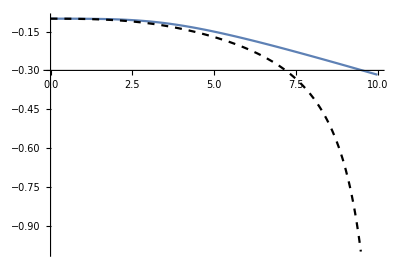

```mathematica
σLocal=0.2;
Show[
ParametricPlot[{rString[t,θMExact[σLocal]],-zString[t,θMExact[σLocal]]},{t,0,10},PlotRange->All,AspectRatio->0.7],
ParametricPlot[{√(xsol[τ,σLocal]^2+ysol[τ,σLocal]^2),-zsol[τ,σLocal]},{τ,0,0.99τM},PlotRange->All,AspectRatio->0.7,PlotStyle->{{Black,Dashed}}]]
```

### Geodesic matching on stringbit trajectories

```mathematica
dxdzGeo[z_,r_]=1/(√(r^2-f[z]))/.AdSSchRules;
```

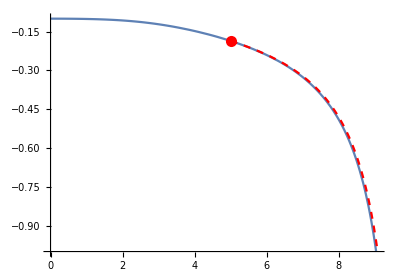

```mathematica
tMatch=5;
σTemp=0.15;
rTemp=Interpolation[Table[{tInt[n],√(xsol[τStatic0[n][σTemp],σTemp]^2+ysol[τStatic0[n][σTemp],σTemp]^2)},{n,1,tNum-tRem-1}]];
zTemp=Interpolation[Table[{tInt[n],zsol[τStatic0[n][σTemp],σTemp]},{n,1,tNum-tRem-1}]];
FLater=zTemp'[tMatch]/rTemp'[tMatch];
RLater=√(FLater^2+f[zTemp[tMatch]]/.AdSSchRules);
LatNullGeo=Table[{rTemp[tMatch]+Re[NIntegrate[dxdzGeo[z,RLater],{z,zTemp[tMatch],zz}]],-zz},{zz,zTemp[tMatch],1,0.01}];
Show[
ParametricPlot[{√(xsol[τ,σTemp]^2+ysol[τ,σTemp]^2),-zsol[τ,σTemp]},{τ,0,0.99τM},PlotRange->All,AspectRatio->0.7],
Graphics[{PointSize->0.02,Red,Point[{rTemp[tMatch],-zTemp[tMatch]}]}],
ListPlot[LatNullGeo,Joined->True,PlotStyle->{Red,Dashed}]]
```

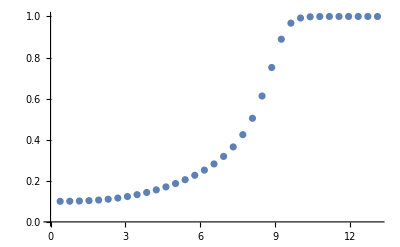

```mathematica
ListPlot[zTemp]
```

### Including the first AdS-Schwarzschild corrections

#### As derived in the notes, the first correction is just 2 z^3

```mathematica
vEoMSch=Derivative[2,0][ζ][t,θ]-2/P0tInitTME[θ]^2*(t^2-ζ[t,θ]^2+(Derivative[0,1][ζ][t,θ])^2)/((z0/.InitialValues)+ζ[t,θ])^5-2*((z0/.InitialValues)+ζ[t,θ])^3;
```

#### The solution breaks down, and that’s okay (we could fix it with EventLocator later). Another note is that we’re using the same boundary conditions as before, and that’s not really consistent now, as we have the z^3 term which is non-zero

```mathematica
vSolSch=NDSolve[Join[{vEoMSch==0},vICBC],ζ,{t,0,100},{θ,θMinME,θMaxME}][[1]];
tBreak=vSolSch[[1,2,1,1,2]]
```

NDSolve::ndsz: At t == 10.0008, step size is effectively zero; singularity or stiff system suspected.

NDSolve::eerr: Warning: scaled local spatial error estimate of 1827.83 at t = 10.0008 in the direction of independent variable θ is much greater than the prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

10.0008

#### The string solutions is still given by the AdS-looking ansatz

```mathematica
rStringSch[t_,θ_]=√(t^2-ζ[t,θ]^2)/.vSolSch;
zStringSch[t_,θ_]=z0+ζ[t,θ]/.vSolSch/.InitialValues;
```

#### Geometrical maximum is

```mathematica
rGeoMax=rGeo[1]-rGeo[z0]/.χzS4->z0^4/.InitialValues;
```

#### Let’s make sure these are well behaved, and let’s compare them to the corresponding actual trajectories

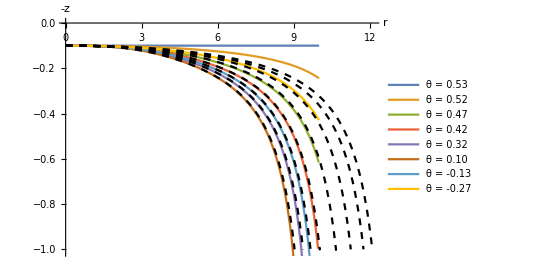

```mathematica
σList={0,0.02,0.05,0.07,0.1,0.15,0.21,0.27};
StringBitsSchPlot=Show[
ParametricPlot[Evaluate[Table[{rStringSch[t,θMExact[σ]],-zStringSch[t,θMExact[σ]]},{σ,σList}]],{t,0,tBreak},
PlotRange->{Automatic,{-1,0}},AspectRatio->0.7,AxesLabel->{"r","-z"},PlotLegends->Placed[Table["θ = "<>ToString[NumberForm[θMExact[σLocal],{3,2}]],{σLocal,σList}],Right]],
ParametricPlot[Table[{√(xsol[τ,σ]^2+ysol[τ,σ]^2),-zsol[τ,σ]},{σ,σList}],{τ,0,0.99τM},AspectRatio->0.7,PlotStyle->{{Black,Dashed}}],PlotRange->{{0,rGeoMax},{-1.01,0}},AxesLabel->{Style["r",FontSize->15],Style["-z",FontSize->15]},
LabelStyle->{Directive[Black,12],FontFamily->"Helvetica"},ImageSize->400]
```

```mathematica
(*Export["../Notes/Images/StringBitsSchPlot.pdf",StringBitsSchPlot]
```

#### That looks great, even though we only included the first correction!

#### Note that the entire evolution stops at some t = t_Break which in our case is 10 -- in the radial direction, the curves are only plotted up to r = 10, because we’re assuming the AdS ansatz in which essentially r = 1*t. This is okay at early times, but then at some point the horizon kicks in and the time slows down for some stringbits. Because of that, the z^3 term is always there (realistically, the horizon would kill it eventually), and the trajectories “slam” back into r = 0

#### Let’s find the stopping distances in a simple way: ask if a particular stringbit trajectory passes z = 1 and if so, find its radial position at that z

```mathematica
AnalStop={};
Do[
If[zStringSch[tBreak,θ]>1,
tFun=t/.FindRoot[zStringSch[t,θ]==1,{t,0.9tBreak,0,tBreak}];
AnalStop=Append[AnalStop,{θ,rStringSch[tFun,θ]}];
]
,{θ,θMinME,θMaxME,(θMaxME-θMinME)/100}]
```

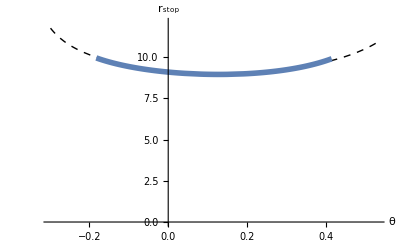

```mathematica
StopDistSch1=Show[
Plot[rStopNum[θ],{θ,θMinME,θMaxME},PlotStyle->{Black,Dashed,Thick}],
ListPlot[AnalStop,Joined->True,PlotStyle->Thickness[0.01]],
PlotRange->{{θMinME,θMaxME},{0,rGeoMax}},AxesOrigin->{0,0},AxesLabel->{Style["θ",FontSize->15],Style["r_stop",FontSize->15]},
LabelStyle->{Directive[Black,12],FontFamily->"Helvetica"},ImageSize->400]
```

```mathematica
(*Export["../Notes/Images/StopDistSch1.pdf",StopDistSch1]
```

#### Let’s now try the other way, similar to what we were doing before: choose some time t_match and extract the corresponding geodesic stopping distances from there

```mathematica
Clear[χzS4];
pzEAdSSch=1/f[z]*√(1-f[z]/R^2)/.R->√(1-χzS4);
pzEAdS=Derivative[1,0][ζ][t,θ]/.t->tS;
χzS4Rule=Solve[pzEAdSSch==pzEAdS,χzS4][[1]];
rStopAlt[tS_,θ_]=(rStringSch[tS,θ]+rGeo[1]-rGeo[z])/.χzS4Rule/.AdSSchRules/.z->zStringSch[tS,θ]/.vSolSch;
```

#### Let’s plot it

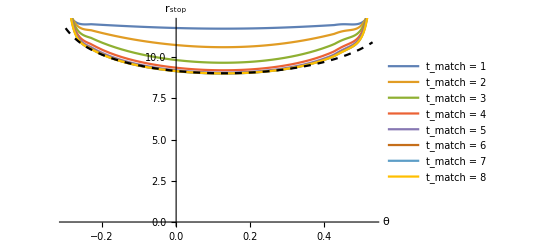

```mathematica
tList=Table[tS,{tS,1,8,1}];
StopDistSch2=Show[
Plot[Evaluate[Table[rStopAlt[tS,θ],{tS,tList}]],{θ,θMinME,θMaxME},AxesOrigin->{0,0},PlotRange->All,PlotLegends->Placed[Table["t_match = "<>ToString[tS],{tS,tList}],Right]],
Plot[rStopNum[θ],{θ,θMinME,θMaxME},PlotStyle->{Black,Dashed}],
PlotRange->{{θMinME,θMaxME},{0,rGeoMax}},AxesOrigin->{0,0},AxesLabel->{Style["θ",FontSize->15],Style["r_stop",FontSize->15]},
LabelStyle->{Directive[Black,12],FontFamily->"Helvetica"},ImageSize->400]
```

```mathematica
(*Export["../Notes/Images/StopDistSch2.pdf",StopDistSch2]
```

```mathematica
Series[rGeo[1]-rGeo[z0]/.χzS4->z0^4,{z0,0,4}]
```

(√π Gamma[5/4])/(Gamma[3/4] z0)-1-z0^4/10+O[z0]^5

```mathematica
(√π Gamma[5/4])/(Gamma[3/4] z0)/.z0->0.1//N
```

13.1103

### Geodesic matching - redux

#### Don’t forget the difference between the approximate and true angle

```mathematica
xDot[n_,σ_]:=Derivative[1,0][xsol][τStatic0[n][σ],σ];
yDot[n_,σ_]:=Derivative[1,0][ysol][τStatic0[n][σ],σ];zDot[n_,σ_]:=Derivative[1,0][zsol][τStatic0[n][σ],σ];
```

```mathematica
rDot[n_,σ_]:=(xsol[τStatic0[n][σ],σ]*xDot[n,σ]+ysol[τStatic0[n][σ],σ]*yDot[n,σ])/(√(xsol[τStatic0[n][σ],σ]^2+ysol[τStatic0[n][σ],σ]^2));
```

```mathematica
χzs4Sol=Solve[rDotSymb/zDotSymb==1/(√(zLoc^4-χzs4Symb)),χzs4Symb][[1]]
```

{χzs4Symb→(-zDotSymb^2+rDotSymb^2 zLoc^4)/rDotSymb^2}

```mathematica
Clear[n]
χzs4[n_,σ_]=χzs4Symb/.χzs4Sol/.zLoc->zsol[τStatic0[n][σ],σ]/.rDotSymb->rDot[n,σ]/.zDotSymb->zDot[n,σ];
```

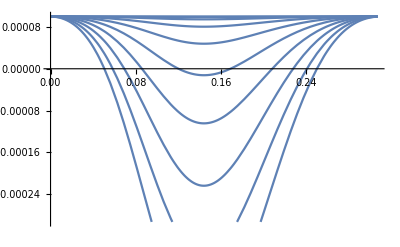

```mathematica
Plot[Table[χzs4[nn,σ],{nn,1,10,1}],{σ,0,σLocKink}]
```

```mathematica
rGeo[z_]=-1/z Hypergeometric2F1[1/4,1/2,5/4,χzS4/z^4];
```

```mathematica
rStopBits[n_,σ_]=(√(xsol[τStatic0[n][σ],σ]^2+ysol[τStatic0[n][σ],σ]^2)+rGeo[1]-rGeo[zsol[τStatic0[n][σ],σ]])/.χzS4->χzs4[n,σ];
```

```mathematica
θMExact[σ]
```

ArcTan[0.075 (-3.98942 ⅇ^(-50. (-0.301619+σ)^2)+7.86704 ⅇ^(-50. (-0.00161861+σ)^2)) Sec[σ]]

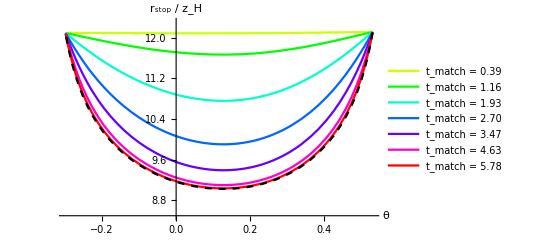

```mathematica
nWant={1,3,5,7,9,12,15};
GeoMatching=Show[
ParametricPlot[Evaluate[Table[{θMExact[σ],rStopBits[n,σ]},{n,nWant}]],{σ,0,σLocKink},PlotRange->{Automatic,{8.5,12.3}},PlotStyle->Table[Hue[0.2+0.8i/(Length[nWant]-1)],{i,0,Length[nWant]-1}],PlotLegends->Placed[Table["t_match = "<>ToString[NumberForm[tInt[n],{3,2}]],{n,nWant}],Right],AspectRatio->0.6],
ParametricPlot[{θMExact[σ],√(xsol[0.99τM,σ]^2+ysol[0.99τM,σ]^2)},{σ,0,σLocKink},PlotStyle->{Black,Dashed},AspectRatio->0.6],AxesLabel->{Style["θ",FontSize->15],Style["r_stop / z_H",FontSize->15]},
LabelStyle->{Directive[Black,12],FontFamily->"Helvetica"},ImageSize->400]
```

```mathematica
(*Export["../Notes/Images/GeoMatching.pdf",GeoMatching]
```

## Looping over IC’s

### Choose the ranges

#### Let’s choose the range of energies on a log scale

{5.62341,7.49894,10,13.3352,17.7828,23.7137,31.6228,42.1697,56.2341,74.9894,100,133.352,177.828,237.137,316.228,421.697,562.341,749.894,1000,1333.52,1778.28,2371.37,3162.28,4216.97,5623.41,7498.94,10000,13335.2,17782.8,23713.7,31622.8,42169.7,56234.1,74989.4,100000,133352.,177828.,237137.,316228.,421697.,562341.,749894.,1000000,1.33352×10^6,1.77828×10^6,2.37137×10^6,3.16228×10^6,4.21697×10^6,5.62341×10^6,7.49894×10^6,10000000}

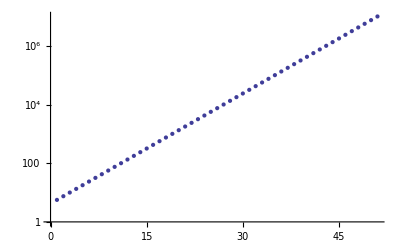

```mathematica
EnList1=Table[10^n,{n,0,7}];
EnList2=Drop[Sort[Join[EnList1,Table[Exp[Log[EnList1[[i-1]]]+(Log[EnList1[[i]]]-Log[EnList1[[i-1]]])/2]//N,{i,2,Length[EnList1]}]]],1];
EnList3=Drop[Sort[Join[EnList2,Table[Exp[Log[EnList2[[i-1]]]+(Log[EnList2[[i]]]-Log[EnList2[[i-1]]])/2]//N,{i,2,Length[EnList2]}]]],1];
EWantList=Sort[Join[EnList3,Table[Exp[Log[EnList3[[i-1]]]+(Log[EnList3[[i]]]-Log[EnList3[[i-1]]])/2]//N,{i,2,Length[EnList3]}]]]
ListLogPlot[EWantList]
```

#### Let’s choose the range of z’s

```mathematica
zList=Table[z0,{z0,0.14,0.02,-0.01}]
```

{0.14,0.13,0.12,0.11,0.1,0.09,0.08,0.07,0.06,0.05,0.04,0.03,0.02}

```mathematica
(*zList={0.16,0.15,0.14,0.13,0.12,0.11};
```

#### This means that we will have at least this many steps in the loop per one angle

```mathematica
Length[zList]*Length[EWantList]
```

663

#### Choose angles in degress

```mathematica
θL={1,10,100};
θDegList=Sort[Join[θL,Table[Exp[Log[θL[[i-1]]]+(Log[θL[[i]]]-Log[θL[[i-1]]])/2]//N,{i,2,Length[θL]}]]]
```

{1,3.16228,10,31.6228,100}

```mathematica
θDegList={1,3.1622776601683795,10};
```

#### But we will terminate the A loop if we determine that both rMin and rMax > rRatio*(geometrical limit)

```mathematica
rRatio=0.95;
```

#### We will record the late time locations of the following interesting points:

```mathematica
σInterest={0,σLocZero,σLocKink,π}
```

{0,0.348506,0.61454,π}

### Main loop

#### Do the big loop

```mathematica
θCnt=1;
```

```mathematica
Do[
Print["Started θ = "<>ToString[θDegLocal]<>" at "<>DateString[]];
EConst=NIntegrate[AsymptoticEnergyDensity/.Tanθ->Tan[θDegLocal/360*2π],{σ,0,π/2}];
ARule={A->z0*EWantTemp/EConst};
Do[
Print["--- Started z0 = "<>ToString[z0Local]<>" at "<>DateString[]];
MasterList={};
Do[
Print["------ Started E = "<>ToString[ELocal]<>" at "<>DateString[]];
(* Set the initial values: *)
ALocal=A/.ARule/.EWantTemp->ELocal/.z0->z0Local;
BLocal=B/.BRule/.Tanθ->Tan[θDegLocal/360*2π]/.A->ALocal/.z0->z0Local;
InitialValues={z0->z0Local,A->ALocal,B->BLocal,τMax->12};
(* Solve the EoMs: *)
Sol=Quiet[NDSolve[{Table[EoMs[[i]]==0,{i,1,dim}],ICBC}/.InitialValues,{t,x1,x2,z},{τ,0,τMax/.InitialValues},{σ,0,π},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->1200}}][[1]]];
τM=Sol[[1,2,1,1,2]];
xsol[τ_,σ_]:=x1[τ,σ]/.Sol;
ysol[τ_,σ_]:=x2[τ,σ]/.Sol;
zsol[τ_,σ_]:=z[τ,σ]/.Sol;
(* Find the minimum r *)
σLocMin=σ/.FindMinimum[{√(xsol[0.99τM,σ]^2+ysol[0.99τM,σ]^2),0≤σ≤σLocKink},σ][[2]];
σInterestLocal=Append[σInterest,σLocMin];
(* Extract relevant data: *)
LocInterest=Table[{xsol[0.99τM,σ],ysol[0.99τM,σ],zsol[0.99τM,σ]},{σ,σInterestLocal}];
MasterList=Append[MasterList,Flatten[{ALocal,BLocal,z0Local,LocInterest},1]];
(* See if you can get out: *)
GeoLimit=(1/zs*(√π*Gamma[5/4])/Gamma[3/4]-Hypergeometric2F1[1/4,1/2,5/4,zs^4])/.zs->z0Local;
rMin=√(xsol[0.99τM,σLocMin]^2+ysol[0.99τM,σLocMin]^2);
rMax=√(xsol[0.99τM,0]^2+ysol[0.99τM,0]^2);
If[rMin/rMax>rRatio&&rMax>rRatio*GeoLimit,Break[]];
,{ELocal,EWantList}];
Export["PaperData/KinkyStringsDeg"<>ToString[θCnt]<>"z0-"<>ToString[z0Local]<>".dat",MasterList];
,{z0Local,zList}];
θCnt=θCnt+1;
,{θDegLocal,θDegList}]
```

Started θ = 1 at Tue 24 Nov 2015 23:59:08

--- Started z0 = 0.14 at Tue 24 Nov 2015 23:59:08

------ Started E = 5.62341 at Tue 24 Nov 2015 23:59:08

------ Started E = 7.49894 at Tue 24 Nov 2015 23:59:15

------ Started E = 10 at Tue 24 Nov 2015 23:59:26

------ Started E = 13.3352 at Tue 24 Nov 2015 23:59:34

------ Started E = 17.7828 at Tue 24 Nov 2015 23:59:42

------ Started E = 23.7137 at Wed 25 Nov 2015 00:00:05

------ Started E = 31.6228 at Wed 25 Nov 2015 00:00:13

------ Started E = 42.1697 at Wed 25 Nov 2015 00:00:27

------ Started E = 56.2341 at Wed 25 Nov 2015 00:00:55

------ Started E = 74.9894 at Wed 25 Nov 2015 00:01:45

------ Started E = 100 at Wed 25 Nov 2015 00:02:04

------ Started E = 133.352 at Wed 25 Nov 2015 00:02:36

------ Started E = 177.828 at Wed 25 Nov 2015 00:02:56

------ Started E = 237.137 at Wed 25 Nov 2015 00:03:02

------ Started E = 316.228 at Wed 25 Nov 2015 00:03:08

------ Started E = 421.697 at Wed 25 Nov 2015 00:03:33

--- Started z0 = 0.13 at Wed 25 Nov 2015 00:03:38

------ Started E = 5.62341 at Wed 25 Nov 2015 00:03:38

------ Started E = 7.49894 at Wed 25 Nov 2015 00:03:45

------ Started E = 10 at Wed 25 Nov 2015 00:03:52

------ Started E = 13.3352 at Wed 25 Nov 2015 00:04:02

------ Started E = 17.7828 at Wed 25 Nov 2015 00:04:11

------ Started E = 23.7137 at Wed 25 Nov 2015 00:04:20

------ Started E = 31.6228 at Wed 25 Nov 2015 00:04:30

------ Started E = 42.1697 at Wed 25 Nov 2015 00:04:43

------ Started E = 56.2341 at Wed 25 Nov 2015 00:05:10

------ Started E = 74.9894 at Wed 25 Nov 2015 00:05:36

------ Started E = 100 at Wed 25 Nov 2015 00:06:09

------ Started E = 133.352 at Wed 25 Nov 2015 00:06:45

------ Started E = 177.828 at Wed 25 Nov 2015 00:07:14

------ Started E = 237.137 at Wed 25 Nov 2015 00:07:50

------ Started E = 316.228 at Wed 25 Nov 2015 00:07:56

------ Started E = 421.697 at Wed 25 Nov 2015 00:08:01

------ Started E = 562.341 at Wed 25 Nov 2015 00:08:13

--- Started z0 = 0.12 at Wed 25 Nov 2015 00:08:18

------ Started E = 5.62341 at Wed 25 Nov 2015 00:08:18

------ Started E = 7.49894 at Wed 25 Nov 2015 00:08:26

------ Started E = 10 at Wed 25 Nov 2015 00:08:37

------ Started E = 13.3352 at Wed 25 Nov 2015 00:08:49

------ Started E = 17.7828 at Wed 25 Nov 2015 00:09:02

------ Started E = 23.7137 at Wed 25 Nov 2015 00:09:11

------ Started E = 31.6228 at Wed 25 Nov 2015 00:09:24

------ Started E = 42.1697 at Wed 25 Nov 2015 00:09:33

------ Started E = 56.2341 at Wed 25 Nov 2015 00:09:47

------ Started E = 74.9894 at Wed 25 Nov 2015 00:10:23

------ Started E = 100 at Wed 25 Nov 2015 00:10:55

------ Started E = 133.352 at Wed 25 Nov 2015 00:11:30

------ Started E = 177.828 at Wed 25 Nov 2015 00:12:05

------ Started E = 237.137 at Wed 25 Nov 2015 00:13:04

------ Started E = 316.228 at Wed 25 Nov 2015 00:13:10

------ Started E = 421.697 at Wed 25 Nov 2015 00:13:29

------ Started E = 562.341 at Wed 25 Nov 2015 00:13:34

------ Started E = 749.894 at Wed 25 Nov 2015 00:13:39

--- Started z0 = 0.11 at Wed 25 Nov 2015 00:13:41

------ Started E = 5.62341 at Wed 25 Nov 2015 00:13:41

------ Started E = 7.49894 at Wed 25 Nov 2015 00:13:47

------ Started E = 10 at Wed 25 Nov 2015 00:13:53

------ Started E = 13.3352 at Wed 25 Nov 2015 00:13:59

------ Started E = 17.7828 at Wed 25 Nov 2015 00:14:11

------ Started E = 23.7137 at Wed 25 Nov 2015 00:14:20

------ Started E = 31.6228 at Wed 25 Nov 2015 00:14:39

------ Started E = 42.1697 at Wed 25 Nov 2015 00:14:46

------ Started E = 56.2341 at Wed 25 Nov 2015 00:15:13

------ Started E = 74.9894 at Wed 25 Nov 2015 00:15:54

------ Started E = 100 at Wed 25 Nov 2015 00:16:27

------ Started E = 133.352 at Wed 25 Nov 2015 00:16:48

------ Started E = 177.828 at Wed 25 Nov 2015 00:17:33

------ Started E = 237.137 at Wed 25 Nov 2015 00:18:05

------ Started E = 316.228 at Wed 25 Nov 2015 00:19:03

------ Started E = 421.697 at Wed 25 Nov 2015 00:19:09

------ Started E = 562.341 at Wed 25 Nov 2015 00:19:27

------ Started E = 749.894 at Wed 25 Nov 2015 00:19:32

--- Started z0 = 0.1 at Wed 25 Nov 2015 00:19:34

------ Started E = 5.62341 at Wed 25 Nov 2015 00:19:34

------ Started E = 7.49894 at Wed 25 Nov 2015 00:19:40

------ Started E = 10 at Wed 25 Nov 2015 00:19:46

------ Started E = 13.3352 at Wed 25 Nov 2015 00:19:52

------ Started E = 17.7828 at Wed 25 Nov 2015 00:20:02

------ Started E = 23.7137 at Wed 25 Nov 2015 00:20:11

------ Started E = 31.6228 at Wed 25 Nov 2015 00:20:19

------ Started E = 42.1697 at Wed 25 Nov 2015 00:20:31

------ Started E = 56.2341 at Wed 25 Nov 2015 00:20:49

------ Started E = 74.9894 at Wed 25 Nov 2015 00:21:17

------ Started E = 100 at Wed 25 Nov 2015 00:21:47

------ Started E = 133.352 at Wed 25 Nov 2015 00:22:14

------ Started E = 177.828 at Wed 25 Nov 2015 00:22:53

------ Started E = 237.137 at Wed 25 Nov 2015 00:23:18

------ Started E = 316.228 at Wed 25 Nov 2015 00:24:07

------ Started E = 421.697 at Wed 25 Nov 2015 00:24:31

------ Started E = 562.341 at Wed 25 Nov 2015 00:24:35

------ Started E = 749.894 at Wed 25 Nov 2015 00:24:40

------ Started E = 1000 at Wed 25 Nov 2015 00:24:43

--- Started z0 = 0.09 at Wed 25 Nov 2015 00:24:45

------ Started E = 5.62341 at Wed 25 Nov 2015 00:24:45

------ Started E = 7.49894 at Wed 25 Nov 2015 00:24:52

------ Started E = 10 at Wed 25 Nov 2015 00:25:00

------ Started E = 13.3352 at Wed 25 Nov 2015 00:25:06

------ Started E = 17.7828 at Wed 25 Nov 2015 00:25:18

------ Started E = 23.7137 at Wed 25 Nov 2015 00:25:31

------ Started E = 31.6228 at Wed 25 Nov 2015 00:25:38

------ Started E = 42.1697 at Wed 25 Nov 2015 00:25:46

------ Started E = 56.2341 at Wed 25 Nov 2015 00:25:56

------ Started E = 74.9894 at Wed 25 Nov 2015 00:26:09

------ Started E = 100 at Wed 25 Nov 2015 00:26:36

------ Started E = 133.352 at Wed 25 Nov 2015 00:27:18

------ Started E = 177.828 at Wed 25 Nov 2015 00:27:50

------ Started E = 237.137 at Wed 25 Nov 2015 00:28:11

------ Started E = 316.228 at Wed 25 Nov 2015 00:28:56

------ Started E = 421.697 at Wed 25 Nov 2015 00:29:30

------ Started E = 562.341 at Wed 25 Nov 2015 00:29:37

------ Started E = 749.894 at Wed 25 Nov 2015 00:29:43

------ Started E = 1000 at Wed 25 Nov 2015 00:29:49

------ Started E = 1333.52 at Wed 25 Nov 2015 00:29:54

------ Started E = 1778.28 at Wed 25 Nov 2015 00:29:58

--- Started z0 = 0.08 at Wed 25 Nov 2015 00:30:03

------ Started E = 5.62341 at Wed 25 Nov 2015 00:30:03

------ Started E = 7.49894 at Wed 25 Nov 2015 00:30:11

------ Started E = 10 at Wed 25 Nov 2015 00:30:20

------ Started E = 13.3352 at Wed 25 Nov 2015 00:30:26

------ Started E = 17.7828 at Wed 25 Nov 2015 00:30:34

------ Started E = 23.7137 at Wed 25 Nov 2015 00:30:45

------ Started E = 31.6228 at Wed 25 Nov 2015 00:30:55

------ Started E = 42.1697 at Wed 25 Nov 2015 00:31:04

------ Started E = 56.2341 at Wed 25 Nov 2015 00:31:13

------ Started E = 74.9894 at Wed 25 Nov 2015 00:31:24

------ Started E = 100 at Wed 25 Nov 2015 00:31:40

------ Started E = 133.352 at Wed 25 Nov 2015 00:32:14

------ Started E = 177.828 at Wed 25 Nov 2015 00:32:52

------ Started E = 237.137 at Wed 25 Nov 2015 00:33:29

------ Started E = 316.228 at Wed 25 Nov 2015 00:34:05

------ Started E = 421.697 at Wed 25 Nov 2015 00:34:40

------ Started E = 562.341 at Wed 25 Nov 2015 00:35:12

------ Started E = 749.894 at Wed 25 Nov 2015 00:35:19

------ Started E = 1000 at Wed 25 Nov 2015 00:35:25

------ Started E = 1333.52 at Wed 25 Nov 2015 00:35:28

------ Started E = 1778.28 at Wed 25 Nov 2015 00:35:31

------ Started E = 2371.37 at Wed 25 Nov 2015 00:35:33

--- Started z0 = 0.07 at Wed 25 Nov 2015 00:35:38

------ Started E = 5.62341 at Wed 25 Nov 2015 00:35:38

------ Started E = 7.49894 at Wed 25 Nov 2015 00:35:46

------ Started E = 10 at Wed 25 Nov 2015 00:35:54

------ Started E = 13.3352 at Wed 25 Nov 2015 00:36:01

------ Started E = 17.7828 at Wed 25 Nov 2015 00:36:08

------ Started E = 23.7137 at Wed 25 Nov 2015 00:36:16

------ Started E = 31.6228 at Wed 25 Nov 2015 00:36:26

------ Started E = 42.1697 at Wed 25 Nov 2015 00:36:36

------ Started E = 56.2341 at Wed 25 Nov 2015 00:36:44

------ Started E = 74.9894 at Wed 25 Nov 2015 00:36:53

------ Started E = 100 at Wed 25 Nov 2015 00:37:06

------ Started E = 133.352 at Wed 25 Nov 2015 00:37:23

------ Started E = 177.828 at Wed 25 Nov 2015 00:38:02

------ Started E = 237.137 at Wed 25 Nov 2015 00:38:46

------ Started E = 316.228 at Wed 25 Nov 2015 00:39:24

------ Started E = 421.697 at Wed 25 Nov 2015 00:40:01

------ Started E = 562.341 at Wed 25 Nov 2015 00:40:36

------ Started E = 749.894 at Wed 25 Nov 2015 00:41:22

------ Started E = 1000 at Wed 25 Nov 2015 00:41:30

------ Started E = 1333.52 at Wed 25 Nov 2015 00:41:37

------ Started E = 1778.28 at Wed 25 Nov 2015 00:41:40

------ Started E = 2371.37 at Wed 25 Nov 2015 00:41:43

------ Started E = 3162.28 at Wed 25 Nov 2015 00:41:46

--- Started z0 = 0.06 at Wed 25 Nov 2015 00:41:52

------ Started E = 5.62341 at Wed 25 Nov 2015 00:41:52

------ Started E = 7.49894 at Wed 25 Nov 2015 00:41:59

------ Started E = 10 at Wed 25 Nov 2015 00:42:08

------ Started E = 13.3352 at Wed 25 Nov 2015 00:42:18

------ Started E = 17.7828 at Wed 25 Nov 2015 00:42:26

------ Started E = 23.7137 at Wed 25 Nov 2015 00:42:33

------ Started E = 31.6228 at Wed 25 Nov 2015 00:42:44

------ Started E = 42.1697 at Wed 25 Nov 2015 00:42:55

------ Started E = 56.2341 at Wed 25 Nov 2015 00:43:04

------ Started E = 74.9894 at Wed 25 Nov 2015 00:43:13

------ Started E = 100 at Wed 25 Nov 2015 00:43:22

------ Started E = 133.352 at Wed 25 Nov 2015 00:43:36

------ Started E = 177.828 at Wed 25 Nov 2015 00:44:08

------ Started E = 237.137 at Wed 25 Nov 2015 00:45:03

------ Started E = 316.228 at Wed 25 Nov 2015 00:45:42

------ Started E = 421.697 at Wed 25 Nov 2015 00:46:18

------ Started E = 562.341 at Wed 25 Nov 2015 00:46:58

------ Started E = 749.894 at Wed 25 Nov 2015 00:47:40

------ Started E = 1000 at Wed 25 Nov 2015 00:48:37

------ Started E = 1333.52 at Wed 25 Nov 2015 00:48:43

------ Started E = 1778.28 at Wed 25 Nov 2015 00:48:48

------ Started E = 2371.37 at Wed 25 Nov 2015 00:48:52

------ Started E = 3162.28 at Wed 25 Nov 2015 00:48:55

------ Started E = 4216.97 at Wed 25 Nov 2015 00:48:58

------ Started E = 5623.41 at Wed 25 Nov 2015 00:49:04

--- Started z0 = 0.05 at Wed 25 Nov 2015 00:49:10

------ Started E = 5.62341 at Wed 25 Nov 2015 00:49:10

------ Started E = 7.49894 at Wed 25 Nov 2015 00:49:17

------ Started E = 10 at Wed 25 Nov 2015 00:49:24

------ Started E = 13.3352 at Wed 25 Nov 2015 00:49:35

------ Started E = 17.7828 at Wed 25 Nov 2015 00:49:42

------ Started E = 23.7137 at Wed 25 Nov 2015 00:49:49

------ Started E = 31.6228 at Wed 25 Nov 2015 00:49:57

------ Started E = 42.1697 at Wed 25 Nov 2015 00:50:09

------ Started E = 56.2341 at Wed 25 Nov 2015 00:50:18

------ Started E = 74.9894 at Wed 25 Nov 2015 00:50:28

------ Started E = 100 at Wed 25 Nov 2015 00:50:37

------ Started E = 133.352 at Wed 25 Nov 2015 00:50:47

------ Started E = 177.828 at Wed 25 Nov 2015 00:51:04

------ Started E = 237.137 at Wed 25 Nov 2015 00:51:22

------ Started E = 316.228 at Wed 25 Nov 2015 00:51:44

------ Started E = 421.697 at Wed 25 Nov 2015 00:52:21

------ Started E = 562.341 at Wed 25 Nov 2015 00:53:03

------ Started E = 749.894 at Wed 25 Nov 2015 00:53:49

------ Started E = 1000 at Wed 25 Nov 2015 00:54:23

------ Started E = 1333.52 at Wed 25 Nov 2015 00:55:11

------ Started E = 1778.28 at Wed 25 Nov 2015 00:55:21

------ Started E = 2371.37 at Wed 25 Nov 2015 00:55:27

------ Started E = 3162.28 at Wed 25 Nov 2015 00:55:31

------ Started E = 4216.97 at Wed 25 Nov 2015 00:55:35

------ Started E = 5623.41 at Wed 25 Nov 2015 00:55:39

------ Started E = 7498.94 at Wed 25 Nov 2015 00:55:44

------ Started E = 10000 at Wed 25 Nov 2015 00:55:51

--- Started z0 = 0.04 at Wed 25 Nov 2015 00:55:58

------ Started E = 5.62341 at Wed 25 Nov 2015 00:55:58

------ Started E = 7.49894 at Wed 25 Nov 2015 00:56:05

------ Started E = 10 at Wed 25 Nov 2015 00:56:13

------ Started E = 13.3352 at Wed 25 Nov 2015 00:56:20

------ Started E = 17.7828 at Wed 25 Nov 2015 00:56:31

------ Started E = 23.7137 at Wed 25 Nov 2015 00:56:38

------ Started E = 31.6228 at Wed 25 Nov 2015 00:56:46

------ Started E = 42.1697 at Wed 25 Nov 2015 00:56:54

------ Started E = 56.2341 at Wed 25 Nov 2015 00:57:04

------ Started E = 74.9894 at Wed 25 Nov 2015 00:57:12

------ Started E = 100 at Wed 25 Nov 2015 00:57:21

------ Started E = 133.352 at Wed 25 Nov 2015 00:57:29

------ Started E = 177.828 at Wed 25 Nov 2015 00:57:41

------ Started E = 237.137 at Wed 25 Nov 2015 00:57:59

------ Started E = 316.228 at Wed 25 Nov 2015 00:58:20

------ Started E = 421.697 at Wed 25 Nov 2015 00:58:42

------ Started E = 562.341 at Wed 25 Nov 2015 00:59:49

------ Started E = 749.894 at Wed 25 Nov 2015 01:00:30

------ Started E = 1000 at Wed 25 Nov 2015 01:01:19

------ Started E = 1333.52 at Wed 25 Nov 2015 01:02:09

------ Started E = 1778.28 at Wed 25 Nov 2015 01:02:56

------ Started E = 2371.37 at Wed 25 Nov 2015 01:03:09

------ Started E = 3162.28 at Wed 25 Nov 2015 01:03:20

------ Started E = 4216.97 at Wed 25 Nov 2015 01:03:25

------ Started E = 5623.41 at Wed 25 Nov 2015 01:03:31

------ Started E = 7498.94 at Wed 25 Nov 2015 01:03:35

------ Started E = 10000 at Wed 25 Nov 2015 01:03:38

------ Started E = 13335.2 at Wed 25 Nov 2015 01:03:46

------ Started E = 17782.8 at Wed 25 Nov 2015 01:03:53

------ Started E = 23713.7 at Wed 25 Nov 2015 01:04:01

------ Started E = 31622.8 at Wed 25 Nov 2015 01:04:04

--- Started z0 = 0.03 at Wed 25 Nov 2015 01:04:11

------ Started E = 5.62341 at Wed 25 Nov 2015 01:04:11

------ Started E = 7.49894 at Wed 25 Nov 2015 01:04:18

------ Started E = 10 at Wed 25 Nov 2015 01:04:28

------ Started E = 13.3352 at Wed 25 Nov 2015 01:04:35

------ Started E = 17.7828 at Wed 25 Nov 2015 01:04:42

------ Started E = 23.7137 at Wed 25 Nov 2015 01:04:49

------ Started E = 31.6228 at Wed 25 Nov 2015 01:04:56

------ Started E = 42.1697 at Wed 25 Nov 2015 01:05:04

------ Started E = 56.2341 at Wed 25 Nov 2015 01:05:12

------ Started E = 74.9894 at Wed 25 Nov 2015 01:05:20

------ Started E = 100 at Wed 25 Nov 2015 01:05:28

------ Started E = 133.352 at Wed 25 Nov 2015 01:05:37

------ Started E = 177.828 at Wed 25 Nov 2015 01:05:45

------ Started E = 237.137 at Wed 25 Nov 2015 01:05:57

------ Started E = 316.228 at Wed 25 Nov 2015 01:06:12

------ Started E = 421.697 at Wed 25 Nov 2015 01:06:30

------ Started E = 562.341 at Wed 25 Nov 2015 01:06:50

------ Started E = 749.894 at Wed 25 Nov 2015 01:07:14

------ Started E = 1000 at Wed 25 Nov 2015 01:07:42

------ Started E = 1333.52 at Wed 25 Nov 2015 01:08:27

------ Started E = 1778.28 at Wed 25 Nov 2015 01:09:25

------ Started E = 2371.37 at Wed 25 Nov 2015 01:10:40

------ Started E = 3162.28 at Wed 25 Nov 2015 01:10:54

------ Started E = 4216.97 at Wed 25 Nov 2015 01:11:36

------ Started E = 5623.41 at Wed 25 Nov 2015 01:11:46

------ Started E = 7498.94 at Wed 25 Nov 2015 01:11:54

------ Started E = 10000 at Wed 25 Nov 2015 01:12:01

------ Started E = 13335.2 at Wed 25 Nov 2015 01:12:06

------ Started E = 17782.8 at Wed 25 Nov 2015 01:12:10

------ Started E = 23713.7 at Wed 25 Nov 2015 01:12:14

------ Started E = 31622.8 at Wed 25 Nov 2015 01:12:22

------ Started E = 42169.7 at Wed 25 Nov 2015 01:12:31

------ Started E = 56234.1 at Wed 25 Nov 2015 01:12:41

------ Started E = 74989.4 at Wed 25 Nov 2015 01:12:49

------ Started E = 100000 at Wed 25 Nov 2015 01:12:55

------ Started E = 133352. at Wed 25 Nov 2015 01:13:03

--- Started z0 = 0.02 at Wed 25 Nov 2015 01:13:08

------ Started E = 5.62341 at Wed 25 Nov 2015 01:13:08

------ Started E = 7.49894 at Wed 25 Nov 2015 01:13:18

------ Started E = 10 at Wed 25 Nov 2015 01:13:24

------ Started E = 13.3352 at Wed 25 Nov 2015 01:13:30

------ Started E = 17.7828 at Wed 25 Nov 2015 01:13:38

------ Started E = 23.7137 at Wed 25 Nov 2015 01:13:47

------ Started E = 31.6228 at Wed 25 Nov 2015 01:13:55

------ Started E = 42.1697 at Wed 25 Nov 2015 01:14:02

------ Started E = 56.2341 at Wed 25 Nov 2015 01:14:08

------ Started E = 74.9894 at Wed 25 Nov 2015 01:14:14

------ Started E = 100 at Wed 25 Nov 2015 01:14:20

------ Started E = 133.352 at Wed 25 Nov 2015 01:14:31

------ Started E = 177.828 at Wed 25 Nov 2015 01:14:39

------ Started E = 237.137 at Wed 25 Nov 2015 01:14:49

------ Started E = 316.228 at Wed 25 Nov 2015 01:14:59

------ Started E = 421.697 at Wed 25 Nov 2015 01:15:10

------ Started E = 562.341 at Wed 25 Nov 2015 01:15:26

------ Started E = 749.894 at Wed 25 Nov 2015 01:15:41

------ Started E = 1000 at Wed 25 Nov 2015 01:16:05

------ Started E = 1333.52 at Wed 25 Nov 2015 01:16:28

------ Started E = 1778.28 at Wed 25 Nov 2015 01:16:56

------ Started E = 2371.37 at Wed 25 Nov 2015 01:17:27

------ Started E = 3162.28 at Wed 25 Nov 2015 01:18:30

------ Started E = 4216.97 at Wed 25 Nov 2015 01:19:42

------ Started E = 5623.41 at Wed 25 Nov 2015 01:20:09

------ Started E = 7498.94 at Wed 25 Nov 2015 01:21:06

------ Started E = 10000 at Wed 25 Nov 2015 01:21:19

------ Started E = 13335.2 at Wed 25 Nov 2015 01:21:30

------ Started E = 17782.8 at Wed 25 Nov 2015 01:21:41

------ Started E = 23713.7 at Wed 25 Nov 2015 01:21:49

------ Started E = 31622.8 at Wed 25 Nov 2015 01:21:56

------ Started E = 42169.7 at Wed 25 Nov 2015 01:22:03

------ Started E = 56234.1 at Wed 25 Nov 2015 01:22:11

------ Started E = 74989.4 at Wed 25 Nov 2015 01:22:19

------ Started E = 100000 at Wed 25 Nov 2015 01:22:27

------ Started E = 133352. at Wed 25 Nov 2015 01:22:40

------ Started E = 177828. at Wed 25 Nov 2015 01:22:52

------ Started E = 237137. at Wed 25 Nov 2015 01:23:00

------ Started E = 316228. at Wed 25 Nov 2015 01:23:10

------ Started E = 421697. at Wed 25 Nov 2015 01:23:17

------ Started E = 562341. at Wed 25 Nov 2015 01:23:21

------ Started E = 749894. at Wed 25 Nov 2015 01:23:26

------ Started E = 1000000 at Wed 25 Nov 2015 01:23:30

Started θ = 3.16228 at Wed 25 Nov 2015 01:23:41

--- Started z0 = 0.14 at Wed 25 Nov 2015 01:23:41

------ Started E = 5.62341 at Wed 25 Nov 2015 01:23:41

------ Started E = 7.49894 at Wed 25 Nov 2015 01:23:48

------ Started E = 10 at Wed 25 Nov 2015 01:23:57

------ Started E = 13.3352 at Wed 25 Nov 2015 01:24:05

------ Started E = 17.7828 at Wed 25 Nov 2015 01:24:18

------ Started E = 23.7137 at Wed 25 Nov 2015 01:24:29

------ Started E = 31.6228 at Wed 25 Nov 2015 01:24:56

------ Started E = 42.1697 at Wed 25 Nov 2015 01:25:23

------ Started E = 56.2341 at Wed 25 Nov 2015 01:25:51

------ Started E = 74.9894 at Wed 25 Nov 2015 01:26:22

------ Started E = 100 at Wed 25 Nov 2015 01:26:31

------ Started E = 133.352 at Wed 25 Nov 2015 01:26:54

------ Started E = 177.828 at Wed 25 Nov 2015 01:27:01

------ Started E = 237.137 at Wed 25 Nov 2015 01:27:07

------ Started E = 316.228 at Wed 25 Nov 2015 01:27:35

------ Started E = 421.697 at Wed 25 Nov 2015 01:28:48

--- Started z0 = 0.13 at Wed 25 Nov 2015 01:28:53

------ Started E = 5.62341 at Wed 25 Nov 2015 01:28:53

------ Started E = 7.49894 at Wed 25 Nov 2015 01:29:00

------ Started E = 10 at Wed 25 Nov 2015 01:29:07

------ Started E = 13.3352 at Wed 25 Nov 2015 01:29:16

------ Started E = 17.7828 at Wed 25 Nov 2015 01:29:26

------ Started E = 23.7137 at Wed 25 Nov 2015 01:29:37

------ Started E = 31.6228 at Wed 25 Nov 2015 01:29:49

------ Started E = 42.1697 at Wed 25 Nov 2015 01:30:29

------ Started E = 56.2341 at Wed 25 Nov 2015 01:31:21

------ Started E = 74.9894 at Wed 25 Nov 2015 01:31:51

------ Started E = 100 at Wed 25 Nov 2015 01:32:01

------ Started E = 133.352 at Wed 25 Nov 2015 01:32:09

------ Started E = 177.828 at Wed 25 Nov 2015 01:32:30

------ Started E = 237.137 at Wed 25 Nov 2015 01:32:35

------ Started E = 316.228 at Wed 25 Nov 2015 01:32:41

------ Started E = 421.697 at Wed 25 Nov 2015 01:33:27

------ Started E = 562.341 at Wed 25 Nov 2015 01:33:31

--- Started z0 = 0.12 at Wed 25 Nov 2015 01:33:33

------ Started E = 5.62341 at Wed 25 Nov 2015 01:33:33

------ Started E = 7.49894 at Wed 25 Nov 2015 01:33:40

------ Started E = 10 at Wed 25 Nov 2015 01:33:48

------ Started E = 13.3352 at Wed 25 Nov 2015 01:33:59

------ Started E = 17.7828 at Wed 25 Nov 2015 01:34:08

------ Started E = 23.7137 at Wed 25 Nov 2015 01:34:19

------ Started E = 31.6228 at Wed 25 Nov 2015 01:34:31

------ Started E = 42.1697 at Wed 25 Nov 2015 01:34:43

------ Started E = 56.2341 at Wed 25 Nov 2015 01:35:23

------ Started E = 74.9894 at Wed 25 Nov 2015 01:35:50

------ Started E = 100 at Wed 25 Nov 2015 01:36:23

------ Started E = 133.352 at Wed 25 Nov 2015 01:36:32

------ Started E = 177.828 at Wed 25 Nov 2015 01:37:03

------ Started E = 237.137 at Wed 25 Nov 2015 01:37:10

------ Started E = 316.228 at Wed 25 Nov 2015 01:37:16

------ Started E = 421.697 at Wed 25 Nov 2015 01:37:22

------ Started E = 562.341 at Wed 25 Nov 2015 01:37:45

------ Started E = 749.894 at Wed 25 Nov 2015 01:37:53

--- Started z0 = 0.11 at Wed 25 Nov 2015 01:37:55

------ Started E = 5.62341 at Wed 25 Nov 2015 01:37:55

------ Started E = 7.49894 at Wed 25 Nov 2015 01:38:03

------ Started E = 10 at Wed 25 Nov 2015 01:38:10

------ Started E = 13.3352 at Wed 25 Nov 2015 01:38:18

------ Started E = 17.7828 at Wed 25 Nov 2015 01:38:25

------ Started E = 23.7137 at Wed 25 Nov 2015 01:38:35

------ Started E = 31.6228 at Wed 25 Nov 2015 01:38:47

------ Started E = 42.1697 at Wed 25 Nov 2015 01:39:00

------ Started E = 56.2341 at Wed 25 Nov 2015 01:39:41

------ Started E = 74.9894 at Wed 25 Nov 2015 01:40:07

------ Started E = 100 at Wed 25 Nov 2015 01:40:41

------ Started E = 133.352 at Wed 25 Nov 2015 01:40:52

------ Started E = 177.828 at Wed 25 Nov 2015 01:41:02

------ Started E = 237.137 at Wed 25 Nov 2015 01:41:46

------ Started E = 316.228 at Wed 25 Nov 2015 01:41:53

------ Started E = 421.697 at Wed 25 Nov 2015 01:41:59

------ Started E = 562.341 at Wed 25 Nov 2015 01:42:05

------ Started E = 749.894 at Wed 25 Nov 2015 01:42:36

--- Started z0 = 0.1 at Wed 25 Nov 2015 01:43:33

------ Started E = 5.62341 at Wed 25 Nov 2015 01:43:33

------ Started E = 7.49894 at Wed 25 Nov 2015 01:43:42

------ Started E = 10 at Wed 25 Nov 2015 01:43:49

------ Started E = 13.3352 at Wed 25 Nov 2015 01:43:55

------ Started E = 17.7828 at Wed 25 Nov 2015 01:44:07

------ Started E = 23.7137 at Wed 25 Nov 2015 01:44:17

------ Started E = 31.6228 at Wed 25 Nov 2015 01:44:28

------ Started E = 42.1697 at Wed 25 Nov 2015 01:44:40

------ Started E = 56.2341 at Wed 25 Nov 2015 01:44:53

------ Started E = 74.9894 at Wed 25 Nov 2015 01:45:36

------ Started E = 100 at Wed 25 Nov 2015 01:46:03

------ Started E = 133.352 at Wed 25 Nov 2015 01:46:51

------ Started E = 177.828 at Wed 25 Nov 2015 01:47:01

------ Started E = 237.137 at Wed 25 Nov 2015 01:47:40

------ Started E = 316.228 at Wed 25 Nov 2015 01:47:47

------ Started E = 421.697 at Wed 25 Nov 2015 01:47:54

------ Started E = 562.341 at Wed 25 Nov 2015 01:47:59

------ Started E = 749.894 at Wed 25 Nov 2015 01:48:05

------ Started E = 1000 at Wed 25 Nov 2015 01:48:24

--- Started z0 = 0.09 at Wed 25 Nov 2015 01:48:29

------ Started E = 5.62341 at Wed 25 Nov 2015 01:48:29

------ Started E = 7.49894 at Wed 25 Nov 2015 01:48:36

------ Started E = 10 at Wed 25 Nov 2015 01:48:48

------ Started E = 13.3352 at Wed 25 Nov 2015 01:48:54

------ Started E = 17.7828 at Wed 25 Nov 2015 01:49:07

------ Started E = 23.7137 at Wed 25 Nov 2015 01:49:15

------ Started E = 31.6228 at Wed 25 Nov 2015 01:49:26

------ Started E = 42.1697 at Wed 25 Nov 2015 01:49:39

------ Started E = 56.2341 at Wed 25 Nov 2015 01:49:53

------ Started E = 74.9894 at Wed 25 Nov 2015 01:50:08

------ Started E = 100 at Wed 25 Nov 2015 01:50:35

------ Started E = 133.352 at Wed 25 Nov 2015 01:51:06

------ Started E = 177.828 at Wed 25 Nov 2015 01:51:18

------ Started E = 237.137 at Wed 25 Nov 2015 01:51:28

------ Started E = 316.228 at Wed 25 Nov 2015 01:51:52

------ Started E = 421.697 at Wed 25 Nov 2015 01:52:01

------ Started E = 562.341 at Wed 25 Nov 2015 01:52:08

------ Started E = 749.894 at Wed 25 Nov 2015 01:52:31

------ Started E = 1000 at Wed 25 Nov 2015 01:52:34

------ Started E = 1333.52 at Wed 25 Nov 2015 01:52:48

------ Started E = 1778.28 at Wed 25 Nov 2015 01:52:52

--- Started z0 = 0.08 at Wed 25 Nov 2015 01:52:55

------ Started E = 5.62341 at Wed 25 Nov 2015 01:52:55

------ Started E = 7.49894 at Wed 25 Nov 2015 01:53:03

------ Started E = 10 at Wed 25 Nov 2015 01:53:11

------ Started E = 13.3352 at Wed 25 Nov 2015 01:53:22

------ Started E = 17.7828 at Wed 25 Nov 2015 01:53:29

------ Started E = 23.7137 at Wed 25 Nov 2015 01:53:37

------ Started E = 31.6228 at Wed 25 Nov 2015 01:53:46

------ Started E = 42.1697 at Wed 25 Nov 2015 01:53:56

------ Started E = 56.2341 at Wed 25 Nov 2015 01:54:08

------ Started E = 74.9894 at Wed 25 Nov 2015 01:54:21

------ Started E = 100 at Wed 25 Nov 2015 01:54:37

------ Started E = 133.352 at Wed 25 Nov 2015 01:55:16

------ Started E = 177.828 at Wed 25 Nov 2015 01:55:58

------ Started E = 237.137 at Wed 25 Nov 2015 01:56:11

------ Started E = 316.228 at Wed 25 Nov 2015 01:56:47

------ Started E = 421.697 at Wed 25 Nov 2015 01:57:36

------ Started E = 562.341 at Wed 25 Nov 2015 01:57:44

------ Started E = 749.894 at Wed 25 Nov 2015 01:58:07

------ Started E = 1000 at Wed 25 Nov 2015 01:58:26

------ Started E = 1333.52 at Wed 25 Nov 2015 01:58:29

------ Started E = 1778.28 at Wed 25 Nov 2015 01:58:36

------ Started E = 2371.37 at Wed 25 Nov 2015 01:58:42

------ Started E = 3162.28 at Wed 25 Nov 2015 01:58:45

--- Started z0 = 0.07 at Wed 25 Nov 2015 01:58:48

------ Started E = 5.62341 at Wed 25 Nov 2015 01:58:48

------ Started E = 7.49894 at Wed 25 Nov 2015 01:58:58

------ Started E = 10 at Wed 25 Nov 2015 01:59:08

------ Started E = 13.3352 at Wed 25 Nov 2015 01:59:16

------ Started E = 17.7828 at Wed 25 Nov 2015 01:59:24

------ Started E = 23.7137 at Wed 25 Nov 2015 01:59:31

------ Started E = 31.6228 at Wed 25 Nov 2015 01:59:40

------ Started E = 42.1697 at Wed 25 Nov 2015 01:59:50

------ Started E = 56.2341 at Wed 25 Nov 2015 02:00:02

------ Started E = 74.9894 at Wed 25 Nov 2015 02:00:14

------ Started E = 100 at Wed 25 Nov 2015 02:00:29

------ Started E = 133.352 at Wed 25 Nov 2015 02:00:48

------ Started E = 177.828 at Wed 25 Nov 2015 02:01:17

------ Started E = 237.137 at Wed 25 Nov 2015 02:02:04

------ Started E = 316.228 at Wed 25 Nov 2015 02:02:27

------ Started E = 421.697 at Wed 25 Nov 2015 02:03:06

------ Started E = 562.341 at Wed 25 Nov 2015 02:03:46

------ Started E = 749.894 at Wed 25 Nov 2015 02:04:06

------ Started E = 1000 at Wed 25 Nov 2015 02:04:11

------ Started E = 1333.52 at Wed 25 Nov 2015 02:04:15

------ Started E = 1778.28 at Wed 25 Nov 2015 02:04:17

------ Started E = 2371.37 at Wed 25 Nov 2015 02:04:24

------ Started E = 3162.28 at Wed 25 Nov 2015 02:04:30

------ Started E = 4216.97 at Wed 25 Nov 2015 02:04:35

------ Started E = 5623.41 at Wed 25 Nov 2015 02:04:38

--- Started z0 = 0.06 at Wed 25 Nov 2015 02:04:40

------ Started E = 5.62341 at Wed 25 Nov 2015 02:04:40

------ Started E = 7.49894 at Wed 25 Nov 2015 02:04:48

------ Started E = 10 at Wed 25 Nov 2015 02:04:59

------ Started E = 13.3352 at Wed 25 Nov 2015 02:05:07

------ Started E = 17.7828 at Wed 25 Nov 2015 02:05:20

------ Started E = 23.7137 at Wed 25 Nov 2015 02:05:27

------ Started E = 31.6228 at Wed 25 Nov 2015 02:05:41

------ Started E = 42.1697 at Wed 25 Nov 2015 02:05:51

------ Started E = 56.2341 at Wed 25 Nov 2015 02:06:02

------ Started E = 74.9894 at Wed 25 Nov 2015 02:06:14

------ Started E = 100 at Wed 25 Nov 2015 02:06:27

------ Started E = 133.352 at Wed 25 Nov 2015 02:06:41

------ Started E = 177.828 at Wed 25 Nov 2015 02:07:00

------ Started E = 237.137 at Wed 25 Nov 2015 02:07:45

------ Started E = 316.228 at Wed 25 Nov 2015 02:08:16

------ Started E = 421.697 at Wed 25 Nov 2015 02:08:30

------ Started E = 562.341 at Wed 25 Nov 2015 02:09:10

------ Started E = 749.894 at Wed 25 Nov 2015 02:10:07

------ Started E = 1000 at Wed 25 Nov 2015 02:10:14

------ Started E = 1333.52 at Wed 25 Nov 2015 02:10:20

------ Started E = 1778.28 at Wed 25 Nov 2015 02:10:24

------ Started E = 2371.37 at Wed 25 Nov 2015 02:10:27

------ Started E = 3162.28 at Wed 25 Nov 2015 02:10:30

------ Started E = 4216.97 at Wed 25 Nov 2015 02:10:36

------ Started E = 5623.41 at Wed 25 Nov 2015 02:10:42

------ Started E = 7498.94 at Wed 25 Nov 2015 02:10:47

------ Started E = 10000 at Wed 25 Nov 2015 02:10:52

------ Started E = 13335.2 at Wed 25 Nov 2015 02:10:56

--- Started z0 = 0.05 at Wed 25 Nov 2015 02:10:59

------ Started E = 5.62341 at Wed 25 Nov 2015 02:10:59

------ Started E = 7.49894 at Wed 25 Nov 2015 02:11:07

------ Started E = 10 at Wed 25 Nov 2015 02:11:14

------ Started E = 13.3352 at Wed 25 Nov 2015 02:11:21

------ Started E = 17.7828 at Wed 25 Nov 2015 02:11:28

------ Started E = 23.7137 at Wed 25 Nov 2015 02:11:35

------ Started E = 31.6228 at Wed 25 Nov 2015 02:11:41

------ Started E = 42.1697 at Wed 25 Nov 2015 02:11:50

------ Started E = 56.2341 at Wed 25 Nov 2015 02:11:59

------ Started E = 74.9894 at Wed 25 Nov 2015 02:12:10

------ Started E = 100 at Wed 25 Nov 2015 02:12:22

------ Started E = 133.352 at Wed 25 Nov 2015 02:12:33

------ Started E = 177.828 at Wed 25 Nov 2015 02:12:48

------ Started E = 237.137 at Wed 25 Nov 2015 02:13:05

------ Started E = 316.228 at Wed 25 Nov 2015 02:13:35

------ Started E = 421.697 at Wed 25 Nov 2015 02:14:10

------ Started E = 562.341 at Wed 25 Nov 2015 02:14:26

------ Started E = 749.894 at Wed 25 Nov 2015 02:15:06

------ Started E = 1000 at Wed 25 Nov 2015 02:16:06

------ Started E = 1333.52 at Wed 25 Nov 2015 02:16:14

------ Started E = 1778.28 at Wed 25 Nov 2015 02:16:21

------ Started E = 2371.37 at Wed 25 Nov 2015 02:16:27

------ Started E = 3162.28 at Wed 25 Nov 2015 02:16:32

------ Started E = 4216.97 at Wed 25 Nov 2015 02:16:35

------ Started E = 5623.41 at Wed 25 Nov 2015 02:16:38

------ Started E = 7498.94 at Wed 25 Nov 2015 02:16:43

------ Started E = 10000 at Wed 25 Nov 2015 02:16:49

------ Started E = 13335.2 at Wed 25 Nov 2015 02:16:53

------ Started E = 17782.8 at Wed 25 Nov 2015 02:16:56

------ Started E = 23713.7 at Wed 25 Nov 2015 02:16:58

------ Started E = 31622.8 at Wed 25 Nov 2015 02:17:03

--- Started z0 = 0.04 at Wed 25 Nov 2015 02:17:06

------ Started E = 5.62341 at Wed 25 Nov 2015 02:17:06

------ Started E = 7.49894 at Wed 25 Nov 2015 02:17:12

------ Started E = 10 at Wed 25 Nov 2015 02:17:20

------ Started E = 13.3352 at Wed 25 Nov 2015 02:17:27

------ Started E = 17.7828 at Wed 25 Nov 2015 02:17:34

------ Started E = 23.7137 at Wed 25 Nov 2015 02:17:40

------ Started E = 31.6228 at Wed 25 Nov 2015 02:17:53

------ Started E = 42.1697 at Wed 25 Nov 2015 02:17:59

------ Started E = 56.2341 at Wed 25 Nov 2015 02:18:10

------ Started E = 74.9894 at Wed 25 Nov 2015 02:18:20

------ Started E = 100 at Wed 25 Nov 2015 02:18:32

------ Started E = 133.352 at Wed 25 Nov 2015 02:18:45

------ Started E = 177.828 at Wed 25 Nov 2015 02:18:59

------ Started E = 237.137 at Wed 25 Nov 2015 02:19:16

------ Started E = 316.228 at Wed 25 Nov 2015 02:19:35

------ Started E = 421.697 at Wed 25 Nov 2015 02:19:59

------ Started E = 562.341 at Wed 25 Nov 2015 02:20:38

------ Started E = 749.894 at Wed 25 Nov 2015 02:20:58

------ Started E = 1000 at Wed 25 Nov 2015 02:21:38

------ Started E = 1333.52 at Wed 25 Nov 2015 02:22:09

------ Started E = 1778.28 at Wed 25 Nov 2015 02:22:40

------ Started E = 2371.37 at Wed 25 Nov 2015 02:22:49

------ Started E = 3162.28 at Wed 25 Nov 2015 02:22:56

------ Started E = 4216.97 at Wed 25 Nov 2015 02:23:02

------ Started E = 5623.41 at Wed 25 Nov 2015 02:23:06

------ Started E = 7498.94 at Wed 25 Nov 2015 02:23:10

------ Started E = 10000 at Wed 25 Nov 2015 02:23:13

------ Started E = 13335.2 at Wed 25 Nov 2015 02:23:19

------ Started E = 17782.8 at Wed 25 Nov 2015 02:23:26

------ Started E = 23713.7 at Wed 25 Nov 2015 02:23:32

------ Started E = 31622.8 at Wed 25 Nov 2015 02:23:38

------ Started E = 42169.7 at Wed 25 Nov 2015 02:23:45

------ Started E = 56234.1 at Wed 25 Nov 2015 02:23:49

------ Started E = 74989.4 at Wed 25 Nov 2015 02:23:52

------ Started E = 100000 at Wed 25 Nov 2015 02:23:55

--- Started z0 = 0.03 at Wed 25 Nov 2015 02:23:58

------ Started E = 5.62341 at Wed 25 Nov 2015 02:23:58

------ Started E = 7.49894 at Wed 25 Nov 2015 02:24:05

------ Started E = 10 at Wed 25 Nov 2015 02:24:12

------ Started E = 13.3352 at Wed 25 Nov 2015 02:24:19

------ Started E = 17.7828 at Wed 25 Nov 2015 02:24:25

------ Started E = 23.7137 at Wed 25 Nov 2015 02:24:32

------ Started E = 31.6228 at Wed 25 Nov 2015 02:24:39

------ Started E = 42.1697 at Wed 25 Nov 2015 02:24:45

------ Started E = 56.2341 at Wed 25 Nov 2015 02:24:58

------ Started E = 74.9894 at Wed 25 Nov 2015 02:25:06

------ Started E = 100 at Wed 25 Nov 2015 02:25:15

------ Started E = 133.352 at Wed 25 Nov 2015 02:25:25

------ Started E = 177.828 at Wed 25 Nov 2015 02:25:37

------ Started E = 237.137 at Wed 25 Nov 2015 02:25:48

------ Started E = 316.228 at Wed 25 Nov 2015 02:26:02

------ Started E = 421.697 at Wed 25 Nov 2015 02:26:20

------ Started E = 562.341 at Wed 25 Nov 2015 02:26:38

------ Started E = 749.894 at Wed 25 Nov 2015 02:27:01

------ Started E = 1000 at Wed 25 Nov 2015 02:27:26

------ Started E = 1333.52 at Wed 25 Nov 2015 02:27:40

------ Started E = 1778.28 at Wed 25 Nov 2015 02:28:14

------ Started E = 2371.37 at Wed 25 Nov 2015 02:28:49

------ Started E = 3162.28 at Wed 25 Nov 2015 02:29:27

------ Started E = 4216.97 at Wed 25 Nov 2015 02:29:37

------ Started E = 5623.41 at Wed 25 Nov 2015 02:29:45

------ Started E = 7498.94 at Wed 25 Nov 2015 02:29:53

------ Started E = 10000 at Wed 25 Nov 2015 02:29:58

------ Started E = 13335.2 at Wed 25 Nov 2015 02:30:03

------ Started E = 17782.8 at Wed 25 Nov 2015 02:30:06

------ Started E = 23713.7 at Wed 25 Nov 2015 02:30:10

------ Started E = 31622.8 at Wed 25 Nov 2015 02:30:14

------ Started E = 42169.7 at Wed 25 Nov 2015 02:30:22

------ Started E = 56234.1 at Wed 25 Nov 2015 02:30:27

------ Started E = 74989.4 at Wed 25 Nov 2015 02:30:32

------ Started E = 100000 at Wed 25 Nov 2015 02:30:37

------ Started E = 133352. at Wed 25 Nov 2015 02:30:42

------ Started E = 177828. at Wed 25 Nov 2015 02:30:48

------ Started E = 237137. at Wed 25 Nov 2015 02:30:54

------ Started E = 316228. at Wed 25 Nov 2015 02:30:56

------ Started E = 421697. at Wed 25 Nov 2015 02:30:59

--- Started z0 = 0.02 at Wed 25 Nov 2015 02:31:02

------ Started E = 5.62341 at Wed 25 Nov 2015 02:31:02

------ Started E = 7.49894 at Wed 25 Nov 2015 02:31:10

------ Started E = 10 at Wed 25 Nov 2015 02:31:17

------ Started E = 13.3352 at Wed 25 Nov 2015 02:31:22

------ Started E = 17.7828 at Wed 25 Nov 2015 02:31:32

------ Started E = 23.7137 at Wed 25 Nov 2015 02:31:41

------ Started E = 31.6228 at Wed 25 Nov 2015 02:31:52

------ Started E = 42.1697 at Wed 25 Nov 2015 02:32:00

------ Started E = 56.2341 at Wed 25 Nov 2015 02:32:07

------ Started E = 74.9894 at Wed 25 Nov 2015 02:32:15

------ Started E = 100 at Wed 25 Nov 2015 02:32:23

------ Started E = 133.352 at Wed 25 Nov 2015 02:32:32

------ Started E = 177.828 at Wed 25 Nov 2015 02:32:41

------ Started E = 237.137 at Wed 25 Nov 2015 02:32:51

------ Started E = 316.228 at Wed 25 Nov 2015 02:33:02

------ Started E = 421.697 at Wed 25 Nov 2015 02:33:13

------ Started E = 562.341 at Wed 25 Nov 2015 02:33:29

------ Started E = 749.894 at Wed 25 Nov 2015 02:33:44

------ Started E = 1000 at Wed 25 Nov 2015 02:34:03

------ Started E = 1333.52 at Wed 25 Nov 2015 02:34:26

------ Started E = 1778.28 at Wed 25 Nov 2015 02:35:05

------ Started E = 2371.37 at Wed 25 Nov 2015 02:35:28

------ Started E = 3162.28 at Wed 25 Nov 2015 02:36:00

------ Started E = 4216.97 at Wed 25 Nov 2015 02:36:42

------ Started E = 5623.41 at Wed 25 Nov 2015 02:37:36

------ Started E = 7498.94 at Wed 25 Nov 2015 02:38:18

------ Started E = 10000 at Wed 25 Nov 2015 02:38:31

------ Started E = 13335.2 at Wed 25 Nov 2015 02:38:42

------ Started E = 17782.8 at Wed 25 Nov 2015 02:38:51

------ Started E = 23713.7 at Wed 25 Nov 2015 02:38:57

------ Started E = 31622.8 at Wed 25 Nov 2015 02:39:02

------ Started E = 42169.7 at Wed 25 Nov 2015 02:39:07

------ Started E = 56234.1 at Wed 25 Nov 2015 02:39:11

------ Started E = 74989.4 at Wed 25 Nov 2015 02:39:27

------ Started E = 100000 at Wed 25 Nov 2015 02:39:35

------ Started E = 133352. at Wed 25 Nov 2015 02:39:51

------ Started E = 177828. at Wed 25 Nov 2015 02:39:59

------ Started E = 237137. at Wed 25 Nov 2015 02:40:08

------ Started E = 316228. at Wed 25 Nov 2015 02:40:15

------ Started E = 421697. at Wed 25 Nov 2015 02:40:20

------ Started E = 562341. at Wed 25 Nov 2015 02:40:24

------ Started E = 749894. at Wed 25 Nov 2015 02:40:36

------ Started E = 1000000 at Wed 25 Nov 2015 02:40:40

------ Started E =           6
1.33352 10 at Wed 25 Nov 2015 02:40:44

------ Started E =           6
1.77828 10 at Wed 25 Nov 2015 02:40:47

------ Started E =           6
2.37137 10 at Wed 25 Nov 2015 02:40:50

------ Started E =           6
3.16228 10 at Wed 25 Nov 2015 02:40:53

------ Started E =           6
4.21697 10 at Wed 25 Nov 2015 02:41:01

------ Started E =           6
5.62341 10 at Wed 25 Nov 2015 02:41:06

------ Started E =           6
7.49894 10 at Wed 25 Nov 2015 02:41:09

------ Started E = 10000000 at Wed 25 Nov 2015 02:41:12

Started θ = 10 at Wed 25 Nov 2015 02:41:16

--- Started z0 = 0.14 at Wed 25 Nov 2015 02:41:16

------ Started E = 5.62341 at Wed 25 Nov 2015 02:41:16

------ Started E = 7.49894 at Wed 25 Nov 2015 02:41:26

------ Started E = 10 at Wed 25 Nov 2015 02:41:36

------ Started E = 13.3352 at Wed 25 Nov 2015 02:41:46

------ Started E = 17.7828 at Wed 25 Nov 2015 02:41:57

------ Started E = 23.7137 at Wed 25 Nov 2015 02:42:09

------ Started E = 31.6228 at Wed 25 Nov 2015 02:42:38

------ Started E = 42.1697 at Wed 25 Nov 2015 02:43:03

------ Started E = 56.2341 at Wed 25 Nov 2015 02:43:30

------ Started E = 74.9894 at Wed 25 Nov 2015 02:44:20

------ Started E = 100 at Wed 25 Nov 2015 02:44:51

------ Started E = 133.352 at Wed 25 Nov 2015 02:45:09

------ Started E = 177.828 at Wed 25 Nov 2015 02:45:15

------ Started E = 237.137 at Wed 25 Nov 2015 02:45:20

------ Started E = 316.228 at Wed 25 Nov 2015 02:45:57

------ Started E = 421.697 at Wed 25 Nov 2015 02:46:51

------ Started E = 562.341 at Wed 25 Nov 2015 02:46:56

--- Started z0 = 0.13 at Wed 25 Nov 2015 02:47:03

------ Started E = 5.62341 at Wed 25 Nov 2015 02:47:03

------ Started E = 7.49894 at Wed 25 Nov 2015 02:47:13

------ Started E = 10 at Wed 25 Nov 2015 02:47:23

------ Started E = 13.3352 at Wed 25 Nov 2015 02:47:33

------ Started E = 17.7828 at Wed 25 Nov 2015 02:47:45

------ Started E = 23.7137 at Wed 25 Nov 2015 02:47:56

------ Started E = 31.6228 at Wed 25 Nov 2015 02:48:30

------ Started E = 42.1697 at Wed 25 Nov 2015 02:48:48

------ Started E = 56.2341 at Wed 25 Nov 2015 02:49:26

------ Started E = 74.9894 at Wed 25 Nov 2015 02:49:54

------ Started E = 100 at Wed 25 Nov 2015 02:50:25

------ Started E = 133.352 at Wed 25 Nov 2015 02:51:01

------ Started E = 177.828 at Wed 25 Nov 2015 02:51:08

------ Started E = 237.137 at Wed 25 Nov 2015 02:51:14

------ Started E = 316.228 at Wed 25 Nov 2015 02:51:20

------ Started E = 421.697 at Wed 25 Nov 2015 02:52:15

------ Started E = 562.341 at Wed 25 Nov 2015 02:52:20

------ Started E = 749.894 at Wed 25 Nov 2015 02:52:23

--- Started z0 = 0.12 at Wed 25 Nov 2015 02:52:26

------ Started E = 5.62341 at Wed 25 Nov 2015 02:52:26

------ Started E = 7.49894 at Wed 25 Nov 2015 02:52:36

------ Started E = 10 at Wed 25 Nov 2015 02:52:46

------ Started E = 13.3352 at Wed 25 Nov 2015 02:52:56

------ Started E = 17.7828 at Wed 25 Nov 2015 02:53:07

------ Started E = 23.7137 at Wed 25 Nov 2015 02:53:19

------ Started E = 31.6228 at Wed 25 Nov 2015 02:53:32

------ Started E = 42.1697 at Wed 25 Nov 2015 02:53:44

------ Started E = 56.2341 at Wed 25 Nov 2015 02:54:00

------ Started E = 74.9894 at Wed 25 Nov 2015 02:54:22

------ Started E = 100 at Wed 25 Nov 2015 02:54:51

------ Started E = 133.352 at Wed 25 Nov 2015 02:55:29

------ Started E = 177.828 at Wed 25 Nov 2015 02:55:58

------ Started E = 237.137 at Wed 25 Nov 2015 02:56:21

------ Started E = 316.228 at Wed 25 Nov 2015 02:56:27

------ Started E = 421.697 at Wed 25 Nov 2015 02:56:33

------ Started E = 562.341 at Wed 25 Nov 2015 02:57:08

------ Started E = 749.894 at Wed 25 Nov 2015 02:57:11

------ Started E = 1000 at Wed 25 Nov 2015 02:57:13

------ Started E = 1333.52 at Wed 25 Nov 2015 02:57:15

--- Started z0 = 0.11 at Wed 25 Nov 2015 02:57:19

------ Started E = 5.62341 at Wed 25 Nov 2015 02:57:19

------ Started E = 7.49894 at Wed 25 Nov 2015 02:57:29

------ Started E = 10 at Wed 25 Nov 2015 02:57:40

------ Started E = 13.3352 at Wed 25 Nov 2015 02:57:50

------ Started E = 17.7828 at Wed 25 Nov 2015 02:58:00

------ Started E = 23.7137 at Wed 25 Nov 2015 02:58:13

------ Started E = 31.6228 at Wed 25 Nov 2015 02:58:24

------ Started E = 42.1697 at Wed 25 Nov 2015 02:58:38

------ Started E = 56.2341 at Wed 25 Nov 2015 02:58:53

------ Started E = 74.9894 at Wed 25 Nov 2015 02:59:30

------ Started E = 100 at Wed 25 Nov 2015 02:59:59

------ Started E = 133.352 at Wed 25 Nov 2015 03:00:29

------ Started E = 177.828 at Wed 25 Nov 2015 03:01:01

------ Started E = 237.137 at Wed 25 Nov 2015 03:01:50

------ Started E = 316.228 at Wed 25 Nov 2015 03:01:57

------ Started E = 421.697 at Wed 25 Nov 2015 03:02:01

------ Started E = 562.341 at Wed 25 Nov 2015 03:02:06

------ Started E = 749.894 at Wed 25 Nov 2015 03:02:34

------ Started E = 1000 at Wed 25 Nov 2015 03:02:37

------ Started E = 1333.52 at Wed 25 Nov 2015 03:02:39

------ Started E = 1778.28 at Wed 25 Nov 2015 03:02:41

--- Started z0 = 0.1 at Wed 25 Nov 2015 03:02:43

------ Started E = 5.62341 at Wed 25 Nov 2015 03:02:43

------ Started E = 7.49894 at Wed 25 Nov 2015 03:02:53

------ Started E = 10 at Wed 25 Nov 2015 03:03:03

------ Started E = 13.3352 at Wed 25 Nov 2015 03:03:13

------ Started E = 17.7828 at Wed 25 Nov 2015 03:03:24

------ Started E = 23.7137 at Wed 25 Nov 2015 03:03:36

------ Started E = 31.6228 at Wed 25 Nov 2015 03:03:47

------ Started E = 42.1697 at Wed 25 Nov 2015 03:04:00

------ Started E = 56.2341 at Wed 25 Nov 2015 03:04:20

------ Started E = 74.9894 at Wed 25 Nov 2015 03:04:36

------ Started E = 100 at Wed 25 Nov 2015 03:05:27

------ Started E = 133.352 at Wed 25 Nov 2015 03:06:03

------ Started E = 177.828 at Wed 25 Nov 2015 03:06:36

------ Started E = 237.137 at Wed 25 Nov 2015 03:07:31

------ Started E = 316.228 at Wed 25 Nov 2015 03:07:36

------ Started E = 421.697 at Wed 25 Nov 2015 03:07:40

------ Started E = 562.341 at Wed 25 Nov 2015 03:07:43

------ Started E = 749.894 at Wed 25 Nov 2015 03:07:49

------ Started E = 1000 at Wed 25 Nov 2015 03:08:12

------ Started E = 1333.52 at Wed 25 Nov 2015 03:08:17

------ Started E = 1778.28 at Wed 25 Nov 2015 03:08:20

------ Started E = 2371.37 at Wed 25 Nov 2015 03:08:22

------ Started E = 3162.28 at Wed 25 Nov 2015 03:08:26

--- Started z0 = 0.09 at Wed 25 Nov 2015 03:08:28

------ Started E = 5.62341 at Wed 25 Nov 2015 03:08:28

------ Started E = 7.49894 at Wed 25 Nov 2015 03:08:37

------ Started E = 10 at Wed 25 Nov 2015 03:08:47

------ Started E = 13.3352 at Wed 25 Nov 2015 03:08:57

------ Started E = 17.7828 at Wed 25 Nov 2015 03:09:08

------ Started E = 23.7137 at Wed 25 Nov 2015 03:09:24

------ Started E = 31.6228 at Wed 25 Nov 2015 03:09:36

------ Started E = 42.1697 at Wed 25 Nov 2015 03:09:48

------ Started E = 56.2341 at Wed 25 Nov 2015 03:10:02

------ Started E = 74.9894 at Wed 25 Nov 2015 03:10:16

------ Started E = 100 at Wed 25 Nov 2015 03:10:43

------ Started E = 133.352 at Wed 25 Nov 2015 03:11:18

------ Started E = 177.828 at Wed 25 Nov 2015 03:11:50

------ Started E = 237.137 at Wed 25 Nov 2015 03:12:42

------ Started E = 316.228 at Wed 25 Nov 2015 03:13:24

------ Started E = 421.697 at Wed 25 Nov 2015 03:13:30

------ Started E = 562.341 at Wed 25 Nov 2015 03:13:33

------ Started E = 749.894 at Wed 25 Nov 2015 03:13:37

------ Started E = 1000 at Wed 25 Nov 2015 03:13:40

------ Started E = 1333.52 at Wed 25 Nov 2015 03:13:47

------ Started E = 1778.28 at Wed 25 Nov 2015 03:13:51

------ Started E = 2371.37 at Wed 25 Nov 2015 03:13:57

------ Started E = 3162.28 at Wed 25 Nov 2015 03:13:59

------ Started E = 4216.97 at Wed 25 Nov 2015 03:14:02

------ Started E = 5623.41 at Wed 25 Nov 2015 03:14:04

--- Started z0 = 0.08 at Wed 25 Nov 2015 03:14:07

------ Started E = 5.62341 at Wed 25 Nov 2015 03:14:07

------ Started E = 7.49894 at Wed 25 Nov 2015 03:14:21

------ Started E = 10 at Wed 25 Nov 2015 03:14:31

------ Started E = 13.3352 at Wed 25 Nov 2015 03:14:40

------ Started E = 17.7828 at Wed 25 Nov 2015 03:14:50

------ Started E = 23.7137 at Wed 25 Nov 2015 03:15:01

------ Started E = 31.6228 at Wed 25 Nov 2015 03:15:12

------ Started E = 42.1697 at Wed 25 Nov 2015 03:15:24

------ Started E = 56.2341 at Wed 25 Nov 2015 03:15:37

------ Started E = 74.9894 at Wed 25 Nov 2015 03:15:50

------ Started E = 100 at Wed 25 Nov 2015 03:16:19

------ Started E = 133.352 at Wed 25 Nov 2015 03:16:48

------ Started E = 177.828 at Wed 25 Nov 2015 03:17:21

------ Started E = 237.137 at Wed 25 Nov 2015 03:17:41

------ Started E = 316.228 at Wed 25 Nov 2015 03:18:27

------ Started E = 421.697 at Wed 25 Nov 2015 03:18:52

------ Started E = 562.341 at Wed 25 Nov 2015 03:18:59

------ Started E = 749.894 at Wed 25 Nov 2015 03:19:03

------ Started E = 1000 at Wed 25 Nov 2015 03:19:07

------ Started E = 1333.52 at Wed 25 Nov 2015 03:19:09

------ Started E = 1778.28 at Wed 25 Nov 2015 03:19:16

------ Started E = 2371.37 at Wed 25 Nov 2015 03:19:20

------ Started E = 3162.28 at Wed 25 Nov 2015 03:19:23

------ Started E = 4216.97 at Wed 25 Nov 2015 03:19:27

------ Started E = 5623.41 at Wed 25 Nov 2015 03:19:31

------ Started E = 7498.94 at Wed 25 Nov 2015 03:19:33

------ Started E = 10000 at Wed 25 Nov 2015 03:19:37

--- Started z0 = 0.07 at Wed 25 Nov 2015 03:19:40

------ Started E = 5.62341 at Wed 25 Nov 2015 03:19:40

------ Started E = 7.49894 at Wed 25 Nov 2015 03:19:50

------ Started E = 10 at Wed 25 Nov 2015 03:19:58

------ Started E = 13.3352 at Wed 25 Nov 2015 03:20:08

------ Started E = 17.7828 at Wed 25 Nov 2015 03:20:18

------ Started E = 23.7137 at Wed 25 Nov 2015 03:20:28

------ Started E = 31.6228 at Wed 25 Nov 2015 03:20:39

------ Started E = 42.1697 at Wed 25 Nov 2015 03:20:52

------ Started E = 56.2341 at Wed 25 Nov 2015 03:21:03

------ Started E = 74.9894 at Wed 25 Nov 2015 03:21:16

------ Started E = 100 at Wed 25 Nov 2015 03:21:30

------ Started E = 133.352 at Wed 25 Nov 2015 03:22:00

------ Started E = 177.828 at Wed 25 Nov 2015 03:22:31

------ Started E = 237.137 at Wed 25 Nov 2015 03:23:13

------ Started E = 316.228 at Wed 25 Nov 2015 03:23:51

------ Started E = 421.697 at Wed 25 Nov 2015 03:24:25

------ Started E = 562.341 at Wed 25 Nov 2015 03:24:56

------ Started E = 749.894 at Wed 25 Nov 2015 03:25:02

------ Started E = 1000 at Wed 25 Nov 2015 03:25:07

------ Started E = 1333.52 at Wed 25 Nov 2015 03:25:11

------ Started E = 1778.28 at Wed 25 Nov 2015 03:25:14

------ Started E = 2371.37 at Wed 25 Nov 2015 03:25:20

------ Started E = 3162.28 at Wed 25 Nov 2015 03:25:26

------ Started E = 4216.97 at Wed 25 Nov 2015 03:25:31

------ Started E = 5623.41 at Wed 25 Nov 2015 03:25:35

------ Started E = 7498.94 at Wed 25 Nov 2015 03:25:41

------ Started E = 10000 at Wed 25 Nov 2015 03:25:45

------ Started E = 13335.2 at Wed 25 Nov 2015 03:25:54

------ Started E = 17782.8 at Wed 25 Nov 2015 03:25:56

--- Started z0 = 0.06 at Wed 25 Nov 2015 03:25:59

------ Started E = 5.62341 at Wed 25 Nov 2015 03:25:59

------ Started E = 7.49894 at Wed 25 Nov 2015 03:26:14

------ Started E = 10 at Wed 25 Nov 2015 03:26:27

------ Started E = 13.3352 at Wed 25 Nov 2015 03:26:36

------ Started E = 17.7828 at Wed 25 Nov 2015 03:26:46

------ Started E = 23.7137 at Wed 25 Nov 2015 03:26:56

------ Started E = 31.6228 at Wed 25 Nov 2015 03:27:06

------ Started E = 42.1697 at Wed 25 Nov 2015 03:27:19

------ Started E = 56.2341 at Wed 25 Nov 2015 03:27:31

------ Started E = 74.9894 at Wed 25 Nov 2015 03:27:42

------ Started E = 100 at Wed 25 Nov 2015 03:27:56

------ Started E = 133.352 at Wed 25 Nov 2015 03:28:10

------ Started E = 177.828 at Wed 25 Nov 2015 03:28:39

------ Started E = 237.137 at Wed 25 Nov 2015 03:29:12

------ Started E = 316.228 at Wed 25 Nov 2015 03:29:34

------ Started E = 421.697 at Wed 25 Nov 2015 03:30:06

------ Started E = 562.341 at Wed 25 Nov 2015 03:31:09

------ Started E = 749.894 at Wed 25 Nov 2015 03:31:46

------ Started E = 1000 at Wed 25 Nov 2015 03:31:53

------ Started E = 1333.52 at Wed 25 Nov 2015 03:31:59

------ Started E = 1778.28 at Wed 25 Nov 2015 03:32:03

------ Started E = 2371.37 at Wed 25 Nov 2015 03:32:07

------ Started E = 3162.28 at Wed 25 Nov 2015 03:32:10

------ Started E = 4216.97 at Wed 25 Nov 2015 03:32:17

------ Started E = 5623.41 at Wed 25 Nov 2015 03:32:22

------ Started E = 7498.94 at Wed 25 Nov 2015 03:32:28

------ Started E = 10000 at Wed 25 Nov 2015 03:32:31

------ Started E = 13335.2 at Wed 25 Nov 2015 03:32:34

------ Started E = 17782.8 at Wed 25 Nov 2015 03:32:37

------ Started E = 23713.7 at Wed 25 Nov 2015 03:32:41

------ Started E = 31622.8 at Wed 25 Nov 2015 03:32:44

------ Started E = 42169.7 at Wed 25 Nov 2015 03:32:47

--- Started z0 = 0.05 at Wed 25 Nov 2015 03:32:51

------ Started E = 5.62341 at Wed 25 Nov 2015 03:32:51

------ Started E = 7.49894 at Wed 25 Nov 2015 03:32:58

------ Started E = 10 at Wed 25 Nov 2015 03:33:13

------ Started E = 13.3352 at Wed 25 Nov 2015 03:33:25

------ Started E = 17.7828 at Wed 25 Nov 2015 03:33:35

------ Started E = 23.7137 at Wed 25 Nov 2015 03:33:44

------ Started E = 31.6228 at Wed 25 Nov 2015 03:33:53

------ Started E = 42.1697 at Wed 25 Nov 2015 03:34:03

------ Started E = 56.2341 at Wed 25 Nov 2015 03:34:14

------ Started E = 74.9894 at Wed 25 Nov 2015 03:34:26

------ Started E = 100 at Wed 25 Nov 2015 03:34:38

------ Started E = 133.352 at Wed 25 Nov 2015 03:34:50

------ Started E = 177.828 at Wed 25 Nov 2015 03:35:05

------ Started E = 237.137 at Wed 25 Nov 2015 03:35:25

------ Started E = 316.228 at Wed 25 Nov 2015 03:36:06

------ Started E = 421.697 at Wed 25 Nov 2015 03:36:22

------ Started E = 562.341 at Wed 25 Nov 2015 03:36:36

------ Started E = 749.894 at Wed 25 Nov 2015 03:37:00

------ Started E = 1000 at Wed 25 Nov 2015 03:37:28

------ Started E = 1333.52 at Wed 25 Nov 2015 03:37:37

------ Started E = 1778.28 at Wed 25 Nov 2015 03:37:44

------ Started E = 2371.37 at Wed 25 Nov 2015 03:37:49

------ Started E = 3162.28 at Wed 25 Nov 2015 03:37:54

------ Started E = 4216.97 at Wed 25 Nov 2015 03:37:57

------ Started E = 5623.41 at Wed 25 Nov 2015 03:38:00

------ Started E = 7498.94 at Wed 25 Nov 2015 03:38:06

------ Started E = 10000 at Wed 25 Nov 2015 03:38:12

------ Started E = 13335.2 at Wed 25 Nov 2015 03:38:18

------ Started E = 17782.8 at Wed 25 Nov 2015 03:38:23

------ Started E = 23713.7 at Wed 25 Nov 2015 03:38:26

------ Started E = 31622.8 at Wed 25 Nov 2015 03:38:29

------ Started E = 42169.7 at Wed 25 Nov 2015 03:38:34

------ Started E = 56234.1 at Wed 25 Nov 2015 03:38:36

------ Started E = 74989.4 at Wed 25 Nov 2015 03:38:39

------ Started E = 100000 at Wed 25 Nov 2015 03:38:41

--- Started z0 = 0.04 at Wed 25 Nov 2015 03:38:43

------ Started E = 5.62341 at Wed 25 Nov 2015 03:38:43

------ Started E = 7.49894 at Wed 25 Nov 2015 03:38:58

------ Started E = 10 at Wed 25 Nov 2015 03:39:12

------ Started E = 13.3352 at Wed 25 Nov 2015 03:39:19

------ Started E = 17.7828 at Wed 25 Nov 2015 03:39:28

------ Started E = 23.7137 at Wed 25 Nov 2015 03:39:37

------ Started E = 31.6228 at Wed 25 Nov 2015 03:39:46

------ Started E = 42.1697 at Wed 25 Nov 2015 03:39:56

------ Started E = 56.2341 at Wed 25 Nov 2015 03:40:06

------ Started E = 74.9894 at Wed 25 Nov 2015 03:40:17

------ Started E = 100 at Wed 25 Nov 2015 03:40:29

------ Started E = 133.352 at Wed 25 Nov 2015 03:40:41

------ Started E = 177.828 at Wed 25 Nov 2015 03:40:53

------ Started E = 237.137 at Wed 25 Nov 2015 03:41:08

------ Started E = 316.228 at Wed 25 Nov 2015 03:41:29

------ Started E = 421.697 at Wed 25 Nov 2015 03:41:59

------ Started E = 562.341 at Wed 25 Nov 2015 03:42:27

------ Started E = 749.894 at Wed 25 Nov 2015 03:42:44

------ Started E = 1000 at Wed 25 Nov 2015 03:43:12

------ Started E = 1333.52 at Wed 25 Nov 2015 03:43:40

------ Started E = 1778.28 at Wed 25 Nov 2015 03:44:12

------ Started E = 2371.37 at Wed 25 Nov 2015 03:44:22

------ Started E = 3162.28 at Wed 25 Nov 2015 03:44:29

------ Started E = 4216.97 at Wed 25 Nov 2015 03:44:36

------ Started E = 5623.41 at Wed 25 Nov 2015 03:44:41

------ Started E = 7498.94 at Wed 25 Nov 2015 03:44:44

------ Started E = 10000 at Wed 25 Nov 2015 03:44:51

------ Started E = 13335.2 at Wed 25 Nov 2015 03:44:55

------ Started E = 17782.8 at Wed 25 Nov 2015 03:45:02

------ Started E = 23713.7 at Wed 25 Nov 2015 03:45:05

------ Started E = 31622.8 at Wed 25 Nov 2015 03:45:09

------ Started E = 42169.7 at Wed 25 Nov 2015 03:45:15

------ Started E = 56234.1 at Wed 25 Nov 2015 03:45:21

------ Started E = 74989.4 at Wed 25 Nov 2015 03:45:26

------ Started E = 100000 at Wed 25 Nov 2015 03:45:29

------ Started E = 133352. at Wed 25 Nov 2015 03:45:32

------ Started E = 177828. at Wed 25 Nov 2015 03:45:36

------ Started E = 237137. at Wed 25 Nov 2015 03:45:39

------ Started E = 316228. at Wed 25 Nov 2015 03:45:42

--- Started z0 = 0.03 at Wed 25 Nov 2015 03:45:45

------ Started E = 5.62341 at Wed 25 Nov 2015 03:45:45

------ Started E = 7.49894 at Wed 25 Nov 2015 03:45:53

------ Started E = 10 at Wed 25 Nov 2015 03:46:00

------ Started E = 13.3352 at Wed 25 Nov 2015 03:46:08

------ Started E = 17.7828 at Wed 25 Nov 2015 03:46:24

------ Started E = 23.7137 at Wed 25 Nov 2015 03:46:33

------ Started E = 31.6228 at Wed 25 Nov 2015 03:46:42

------ Started E = 42.1697 at Wed 25 Nov 2015 03:46:51

------ Started E = 56.2341 at Wed 25 Nov 2015 03:47:01

------ Started E = 74.9894 at Wed 25 Nov 2015 03:47:10

------ Started E = 100 at Wed 25 Nov 2015 03:47:22

------ Started E = 133.352 at Wed 25 Nov 2015 03:47:33

------ Started E = 177.828 at Wed 25 Nov 2015 03:47:45

------ Started E = 237.137 at Wed 25 Nov 2015 03:47:59

------ Started E = 316.228 at Wed 25 Nov 2015 03:48:12

------ Started E = 421.697 at Wed 25 Nov 2015 03:48:31

------ Started E = 562.341 at Wed 25 Nov 2015 03:48:51

------ Started E = 749.894 at Wed 25 Nov 2015 03:49:17

------ Started E = 1000 at Wed 25 Nov 2015 03:49:36

------ Started E = 1333.52 at Wed 25 Nov 2015 03:49:53

------ Started E = 1778.28 at Wed 25 Nov 2015 03:50:23

------ Started E = 2371.37 at Wed 25 Nov 2015 03:50:59

------ Started E = 3162.28 at Wed 25 Nov 2015 03:51:59

------ Started E = 4216.97 at Wed 25 Nov 2015 03:52:11

------ Started E = 5623.41 at Wed 25 Nov 2015 03:52:21

------ Started E = 7498.94 at Wed 25 Nov 2015 03:52:29

------ Started E = 10000 at Wed 25 Nov 2015 03:52:35

------ Started E = 13335.2 at Wed 25 Nov 2015 03:53:20

------ Started E = 17782.8 at Wed 25 Nov 2015 03:53:27

------ Started E = 23713.7 at Wed 25 Nov 2015 03:53:34

------ Started E = 31622.8 at Wed 25 Nov 2015 03:53:38

------ Started E = 42169.7 at Wed 25 Nov 2015 03:53:42

------ Started E = 56234.1 at Wed 25 Nov 2015 03:53:46

------ Started E = 74989.4 at Wed 25 Nov 2015 03:53:52

------ Started E = 100000 at Wed 25 Nov 2015 03:53:56

------ Started E = 133352. at Wed 25 Nov 2015 03:54:02

------ Started E = 177828. at Wed 25 Nov 2015 03:54:06

------ Started E = 237137. at Wed 25 Nov 2015 03:54:11

------ Started E = 316228. at Wed 25 Nov 2015 03:54:14

------ Started E = 421697. at Wed 25 Nov 2015 03:54:17

------ Started E = 562341. at Wed 25 Nov 2015 03:54:22

------ Started E = 749894. at Wed 25 Nov 2015 03:54:25

------ Started E = 1000000 at Wed 25 Nov 2015 03:54:28

------ Started E =           6
1.33352 10 at Wed 25 Nov 2015 03:54:30

--- Started z0 = 0.02 at Wed 25 Nov 2015 03:54:34

------ Started E = 5.62341 at Wed 25 Nov 2015 03:54:34

------ Started E = 7.49894 at Wed 25 Nov 2015 03:54:43

------ Started E = 10 at Wed 25 Nov 2015 03:54:54

------ Started E = 13.3352 at Wed 25 Nov 2015 03:55:02

------ Started E = 17.7828 at Wed 25 Nov 2015 03:55:10

------ Started E = 23.7137 at Wed 25 Nov 2015 03:55:27

------ Started E = 31.6228 at Wed 25 Nov 2015 03:55:35

------ Started E = 42.1697 at Wed 25 Nov 2015 03:55:43

------ Started E = 56.2341 at Wed 25 Nov 2015 03:55:52

------ Started E = 74.9894 at Wed 25 Nov 2015 03:56:01

------ Started E = 100 at Wed 25 Nov 2015 03:56:10

------ Started E = 133.352 at Wed 25 Nov 2015 03:56:19

------ Started E = 177.828 at Wed 25 Nov 2015 03:56:29

------ Started E = 237.137 at Wed 25 Nov 2015 03:56:41

------ Started E = 316.228 at Wed 25 Nov 2015 03:56:52

------ Started E = 421.697 at Wed 25 Nov 2015 03:57:04

------ Started E = 562.341 at Wed 25 Nov 2015 03:57:18

------ Started E = 749.894 at Wed 25 Nov 2015 03:57:34

------ Started E = 1000 at Wed 25 Nov 2015 03:57:54

------ Started E = 1333.52 at Wed 25 Nov 2015 03:58:10

------ Started E = 1778.28 at Wed 25 Nov 2015 03:58:30

------ Started E = 2371.37 at Wed 25 Nov 2015 03:58:53

------ Started E = 3162.28 at Wed 25 Nov 2015 03:59:11

------ Started E = 4216.97 at Wed 25 Nov 2015 03:59:52

------ Started E = 5623.41 at Wed 25 Nov 2015 04:01:00

------ Started E = 7498.94 at Wed 25 Nov 2015 04:02:10

------ Started E = 10000 at Wed 25 Nov 2015 04:02:24

------ Started E = 13335.2 at Wed 25 Nov 2015 04:02:35

------ Started E = 17782.8 at Wed 25 Nov 2015 04:02:44

------ Started E = 23713.7 at Wed 25 Nov 2015 04:02:52

------ Started E = 31622.8 at Wed 25 Nov 2015 04:02:57

------ Started E = 42169.7 at Wed 25 Nov 2015 04:03:01

------ Started E = 56234.1 at Wed 25 Nov 2015 04:03:06

------ Started E = 74989.4 at Wed 25 Nov 2015 04:03:16

------ Started E = 100000 at Wed 25 Nov 2015 04:03:25

------ Started E = 133352. at Wed 25 Nov 2015 04:03:34

------ Started E = 177828. at Wed 25 Nov 2015 04:03:44

------ Started E = 237137. at Wed 25 Nov 2015 04:03:52

------ Started E = 316228. at Wed 25 Nov 2015 04:03:59

------ Started E = 421697. at Wed 25 Nov 2015 04:04:06

------ Started E = 562341. at Wed 25 Nov 2015 04:04:09

------ Started E = 749894. at Wed 25 Nov 2015 04:04:17

------ Started E = 1000000 at Wed 25 Nov 2015 04:04:22

------ Started E =           6
1.33352 10 at Wed 25 Nov 2015 04:04:26

------ Started E =           6
1.77828 10 at Wed 25 Nov 2015 04:04:30

------ Started E =           6
2.37137 10 at Wed 25 Nov 2015 04:04:33

------ Started E =           6
3.16228 10 at Wed 25 Nov 2015 04:04:37

------ Started E =           6
4.21697 10 at Wed 25 Nov 2015 04:04:42

------ Started E =           6
5.62341 10 at Wed 25 Nov 2015 04:04:50

------ Started E =           6
7.49894 10 at Wed 25 Nov 2015 04:04:53

------ Started E = 10000000 at Wed 25 Nov 2015 04:04:56

## Load and clean up data

### Set parameters

#### Locate the σ-position of the kink and the zero in the y-velocity profile (dashed black lines in the next plot)

```mathematica
σLocKink=x/.FindMinimum[yVelProf[x]/.B->1,{x,0.4}][[2]]
σLocZero=x/.FindRoot[(yVelProf[x]/.B->1)==0,{x,0.2}]
```

0.61454

0.348506

#### The rule for B, once an angle is fixed

```mathematica
TanEndpoint=(Derivative[1,0][x2][0,σ]/.ICVelRules/.σ->0)/(Derivative[1,0][x1][0,σ]/.ICVelRules/.σ->0);
TanKink=-(Derivative[1,0][x2][0,σ]/.ICVelRules/.σ->σLocKink)/(Derivative[1,0][x1][0,σ]/.ICVelRules/.σ->σLocKink);
```

#### Geometrical limit for a given zs

```mathematica
MaxΔx=1/zs*(√π*Gamma[5/4])/Gamma[3/4]-Hypergeometric2F1[1/4,1/2,5/4,zs^4];
```

#### Cut off for z

```mathematica
z0CutOff=0.5;
```

### Load data

#### How many angles:

```mathematica
NumAngles=3;
```

#### Get all the filenames pertaining to a particular angle

```mathematica
SetDirectory[NotebookDirectory[]];
Deg1Files=FileNames["KinkyStringsDeg1*",{"PaperData"}];
Deg2Files=FileNames["KinkyStringsDeg2*",{"PaperData"}];
Deg3Files=FileNames["KinkyStringsDeg3*",{"PaperData"}];
```

#### Manual correction to have z0’s appearing in the file list in the ascending order (not using anymore)

```mathematica
(*Deg1Files=Drop[Insert[Deg1Files,Deg1Files[[Length[Deg1Files]]],9],-1];
Deg2Files=Drop[Insert[Deg2Files,Deg2Files[[Length[Deg2Files]]],9],-1];
Deg3Files=Drop[Insert[Deg3Files,Deg3Files[[Length[Deg3Files]-1]],9],{-2,-2}];
```

#### Join them all together in three big lists

```mathematica
Angle1Raw={};Angle2Raw={};Angle3Raw={};
Do[Angle1Raw=Join[Angle1Raw,Import[Deg1Files[[i]]]];,{i,1,Length[Deg1Files]}]
Do[Angle2Raw=Join[Angle2Raw,Import[Deg2Files[[i]]]];,{i,1,Length[Deg2Files]}]
Do[Angle3Raw=Join[Angle3Raw,Import[Deg3Files[[i]]]];,{i,1,Length[Deg3Files]}]
```

#### Convert them into numerical data

```mathematica
Angle1={};
Do[
ML=Angle1Raw[[i]];
Loc={ML[[1]],ML[[2]],ML[[3]]};
Thg=4;
Do[
CleanVals=ToExpression[StringReplace[{ML[[Thg]],ML[[Thg+1]],ML[[Thg+2]]},{"{"->"","}"->"",","->""}]];
Loc=Append[Loc,CleanVals];
Thg=Thg+3;
,{j,1,5}];
Angle1=Append[Angle1,Loc];
,{i,1,Length[Angle1Raw]}]
```

```mathematica
Angle2={};
Do[
ML=Angle2Raw[[i]];
Loc={ML[[1]],ML[[2]],ML[[3]]};
Thg=4;
Do[
CleanVals=ToExpression[StringReplace[{ML[[Thg]],ML[[Thg+1]],ML[[Thg+2]]},{"{"->"","}"->"",","->""}]];
Loc=Append[Loc,CleanVals];
Thg=Thg+3;
,{j,1,5}];
Angle2=Append[Angle2,Loc];
,{i,1,Length[Angle2Raw]}]
```

```mathematica
Angle3={};
Do[
ML=Angle3Raw[[i]];
Loc={ML[[1]],ML[[2]],ML[[3]]};
Thg=4;
Do[
CleanVals=ToExpression[StringReplace[{ML[[Thg]],ML[[Thg+1]],ML[[Thg+2]]},{"{"->"","}"->"",","->""}]];
Loc=Append[Loc,CleanVals];
Thg=Thg+3;
,{j,1,5}];
Angle3=Append[Angle3,Loc];
,{i,1,Length[Angle3Raw]}]
```

### Get actual angles

```mathematica
Do[
MyAngle=ToExpression["Angle"<>ToString[i]];
θqList=Table[ArcTan[(Derivative[1,0][x2][0,σ]/.ICVelRules/.σ->0)/(Derivative[1,0][x1][0,σ]/.ICVelRules/.σ->0)/.A->MyAngle[[i,1]]/.B->MyAngle[[i,2]]/.z0->MyAngle[[i,3]]],{i,1,Length[MyAngle]}];
θgList=Table[ArcTan[(Derivative[1,0][x2][0,σ]/.ICVelRules/.σ->σLocKink)/(Derivative[1,0][x1][0,σ]/.ICVelRules/.σ->σLocKink)/.A->MyAngle[[i,1]]/.B->MyAngle[[i,2]]/.z0->MyAngle[[i,3]]],{i,1,Length[MyAngle]}];
AngleTest[i]=((Abs[θgList]+Abs[θqList])*360/(2π));
RealAngle[i]=((Abs[θgList]+Abs[θqList])*360/(2π))[[1]];
,{i,1,NumAngles,1}]
```

```mathematica
Table[{Min[AngleTest[i]],Max[AngleTest[i]]},{i,1,NumAngles,1}]
```

{{1.,1.},{3.16228,3.16228},{10.,10.}}

```mathematica
Table[RealAngle[i],{i,1,NumAngles,1}]
```

{1.,3.16228,10.}

## Plotting

### rQuark left / rQuark right

#### Available angles

```mathematica
Table[RealAngle[i],{i,1,NumAngles,1}]
```

{1.,3.16228,10.}

#### Notes on saved data

```mathematica
(*σInterest={0,σLocZero,σLocKink,π};
σInterestLocal=Append[σInterest,σLocMin];
LocInterest=Table[{xsol[0.99τM,σ],ysol[0.99τM,σ],zsol[0.99τM,σ]},{σ,σInterestLocal}];
MasterList=Append[MasterList,Flatten[{ALocal,BLocal,z0Local,LocInterest},1]];
```

#### Get all the data for all the angles

```mathematica
Do[
MyAngle=ToExpression["Angle"<>ToString[iiLocal]];
KinkyData[iiLocal]={};
NormalData[iiLocal]={};
Do[
ALocal=MyAngle[[i,1]];
BLocal=MyAngle[[i,2]];
z0Local=MyAngle[[i,3]];
InitialEnergyDensity=-π*√-deth*Πμa[{1,1}]/.τf->1/(2π)/.StretchingRule/.AdSSchRules/.τ->0/.ICVelRules/.ICPosRules/.tpRule/.A->ALocal/.B->BLocal/.z0->z0Local;
EnergyKinkyHalf=NIntegrate[InitialEnergyDensity,{σ,0,π/2}];
EnergyNormalHalf=NIntegrate[InitialEnergyDensity,{σ,π/2,π}];
rQuarkKinky=√(MyAngle[[i,4,1]]^2+MyAngle[[i,4,2]]^2);
rQuarkNormal=√(MyAngle[[i,7,1]]^2+MyAngle[[i,7,2]]^2);
zQuarkKinky=MyAngle[[i,4,3]];
zQuarkNormal=MyAngle[[i,7,3]];
If[zQuarkKinky>z0CutOff&&zQuarkNormal>z0CutOff,
{KinkyData[iiLocal]=Append[KinkyData[iiLocal],{EnergyKinkyHalf,rQuarkKinky,z0Local}];
NormalData[iiLocal]=Append[NormalData[iiLocal],{EnergyNormalHalf,rQuarkNormal,z0Local}];
}];
,{i,1,Length[MyAngle]}];
KinkyDataOrdered[iiLocal]=GatherBy[KinkyData[iiLocal],#[[3]]&];
NormalDataOrdered[iiLocal]=GatherBy[NormalData[iiLocal],#[[3]]&];
,{iiLocal,1,NumAngles,1}]
```

#### z0’s we have

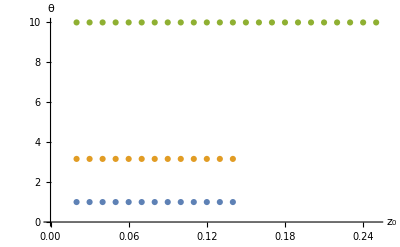

```mathematica
Do[
z0List[iAngle]=Table[KinkyDataOrdered[iAngle][[i,1,3]],{i,1,Length[KinkyDataOrdered[iAngle]]}],
{iAngle,1,NumAngles}];
ListPlot[Table[Table[{z0List[iAngle][[i]],RealAngle[iAngle]},{i,1,Length[z0List[iAngle]]}],{iAngle,1,NumAngles}],AxesLabel->{"z_0","θ"}]
```

#### Interpolate all the data and define the ratios

```mathematica
Do[
Do[
rKinkyInt=Interpolation[KinkyDataOrdered[iAngle][[iLocal]][[All,{1,2}]]];
rNormalInt=Interpolation[NormalDataOrdered[iAngle][[iLocal]][[All,{1,2}]]];
rRatioInt[iAngle,iLocal][En_]=rNormalInt[En]/rKinkyInt[En];
rRatMax[iAngle,iLocal]=Min[{rKinkyInt[[1,1,2]],rNormalInt[[1,1,2]]}];
rRatMin[iAngle,iLocal]=Max[{rKinkyInt[[1,1,1]],rNormalInt[[1,1,1]]}];
,{iLocal,1,Length[KinkyDataOrdered[iAngle]]}]
,{iAngle,1,NumAngles,1}]
```

#### Default choice for which z0’s to consider

```mathematica
Do[
z0ToPlot[iAngle]=Table[iLocal,{iLocal,1,Length[KinkyDataOrdered[iAngle]]}];
,{iAngle,1,NumAngles,1}]
```

#### However, if they don’t turn out to look nice, get rid of some of them

```mathematica
z0ToPlot[1]={2,3,4,5,6,7,8,9,10,11,12,13};
z0ToPlot[2]={2,3,4,5,6,7,8,9,10,11,12,13};
z0ToPlot[3]={2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24};
```

#### Colors I want to assign to angles

```mathematica
ColorList={4,3,1};
```

#### Generate the plot for each angle

```mathematica
Do[
RatPlot[iAngle]=Show[Table[LogLinearPlot[rRatioInt[iAngle,iLocal][En],{En,rRatMin[iAngle,iLocal],rRatMax[iAngle,iLocal]},PlotStyle->{Thick,ColorData[97,"ColorList"][[ColorList[[iAngle]]]],Opacity[1]}],{iLocal,z0ToPlot[iAngle]}],
PlotRange->{{Log[10],Log[10^6]},{0.99,2.4}},Axes->False,Frame->True,RotateLabel->True,LabelStyle->{Directive[Black,14],FontFamily->"Helvetica"},ImageSize->600,
FrameLabel->{Style["E / (λ^(1/2)T)",FontSize->18,Italic,Bold],Style["r_(endpoint, left) / r_(endpoint, right)",FontSize->18,Italic,Bold]}];
,{iAngle,1,NumAngles,1}]
```

#### Show them all together, with annotations

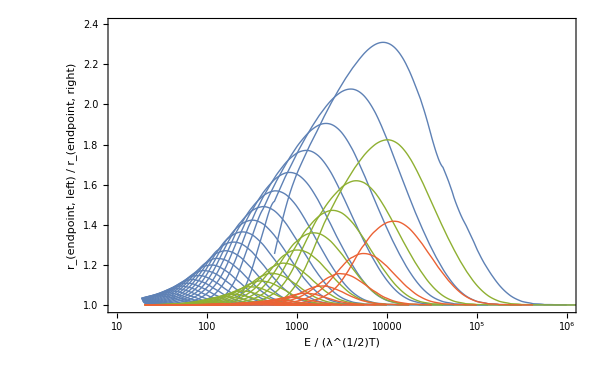

```mathematica
RPlot=Show[Table[RatPlot[iAngle],{iAngle,NumAngles,1,-1}]]
```

### Extract envelopes

#### First run the previous section that generates the interpolated ratios

#### Angles in radians

```mathematica
AngleListRad=Table[RealAngle[i],{i,1,NumAngles,1}]*(2π)/360;
```

#### Find the leftmost ratios that we have -- we shouldn’t take critical ratios less than the maximum of this list

```mathematica
LeftMostRatios={};
Do[
EnergyMinimas=Table[rRatMin[iAngle,iLocal],{iLocal,z0ToPlot[iAngle]}];
iLocMin=z0ToPlot[iAngle][[Ordering[EnergyMinimas][[1]]]];
LeftMostRatios=Append[LeftMostRatios,rRatioInt[iAngle,iLocMin][rRatMin[iAngle,iLocMin]]];
,{iAngle,1,NumAngles}]
LeftMostRatios
```

{1.0001,1.00096,1.03348}

#### Based on the previous, define the criteria

```mathematica
RatCritList=Table[RatCrit,{RatCrit,1.04,1.1,0.01}]
```

{1.04,1.05,1.06,1.07,1.08,1.09,1.1}

#### Extract the envelopes

```mathematica
Cnt=0;
ProgressIndicator[Dynamic[RatCrit],{Min[RatCritList],Max[RatCritList]}]
Do[
Cnt=Cnt+1;
Do[
MinValList[iAngleLoc]={};
Do[
MaxInfo=NMaximize[{rRatioInt[iAngleLoc,iLocal][En],En>rRatMin[iAngleLoc,iLocal],En<rRatMax[iAngleLoc,iLocal]},En];
RatMaxVal=MaxInfo[[1]];
EnMaxVal=En/.MaxInfo[[2]];
If[RatMaxVal>RatCrit&&rRatioInt[iAngleLoc,iLocal][rRatMin[iAngleLoc,iLocal]]<RatCrit,
{EnSol=En/.FindRoot[rRatioInt[iAngleLoc,iLocal][En]==RatCrit,{En,rRatMin[iAngleLoc,iLocal]+(EnMaxVal-rRatMin[iAngleLoc,iLocal])/2,rRatMin[iAngleLoc,iLocal],EnMaxVal}];
MinValList[iAngleLoc]=Append[MinValList[iAngleLoc],EnSol];}
];
,{iLocal,z0ToPlot[iAngleLoc]}];
If[MinValList[iAngleLoc]=={},MinValList[iAngleLoc]={rRatMin[iAngleLoc,z0ToPlot[iAngleLoc][[1]]]}]
,{iAngleLoc,1,NumAngles}];
FL[Cnt]=Table[{Min[MinValList[iAngle]],1/AngleListRad[[iAngle]]},{iAngle,1,NumAngles}];
,{RatCrit,RatCritList}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::reged: The point {181.162} is at the edge of the search region {181.162, 3959.83} in coordinate 1 and the computed search direction points outside the region.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::reged: The point {181.162} is at the edge of the search region {181.162, 3959.83} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot :: reged will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

#### Check that the envelopes look okay

```mathematica
Do[
Cnt=0;
Envelope[iAngle]={};
Do[
Cnt=Cnt+1;
EnVal=FL[Cnt][[iAngle,1]];
Envelope[iAngle]=Append[Envelope[iAngle],{EnVal,RatCrit}];
,{RatCrit,RatCritList}]
,{iAngle,1,NumAngles}]
```

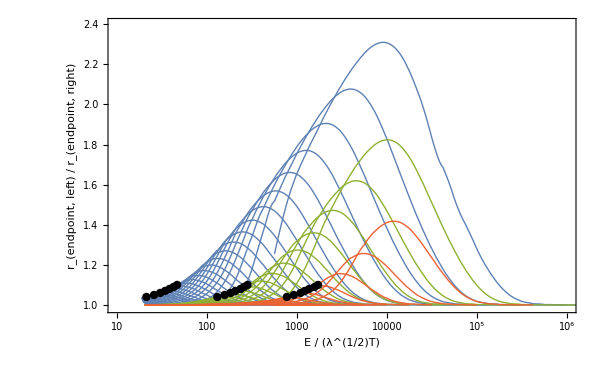

```mathematica
Show[RPlot,Table[ListLogLinearPlot[Envelope[iAngle],Joined->True,Mesh->Full,PlotStyle->Black],{iAngle,1,NumAngles}]]
```

#### Plot 1 / θ vs energy

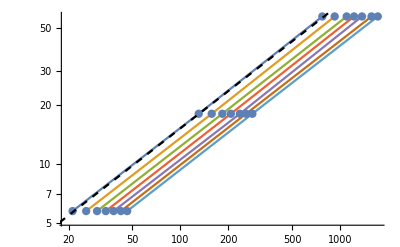

```mathematica
Show[ListLogLogPlot[Table[FL[i],{i,1,Length[RatCritList]}],Joined->True,Mesh->Full],LogLogPlot[0.8 x^0.64,{x,1,2000},PlotStyle->{Black,Dashed}]]
```

#### Extract the relevant data to a file

```mathematica
ICData={μ1,σ1,μ2,σ2};
ThetaEnData=Table[FL[i],{i,1,Length[RatCritList]}];
ForExport=Join[{ICData},{RatCritList},{ThetaEnData}]
Export["FinalPlotData/IC1.m",ForExport];
```

{{0,0.2,0.6,0.2},{1.04,1.05,1.06,1.07,1.08,1.09,1.1},{{{772.046,57.2958},{130.27,18.1185},{21.2076,5.72958}},{{922.016,57.2958},{157.032,18.1185},{25.787,5.72958}},{{1095.63,57.2958},{183.017,18.1185},{30.1676,5.72958}},{{1218.63,57.2958},{206.888,18.1185},{34.1973,5.72958}},{{1366.02,57.2958},{235.558,18.1185},{38.2557,5.72958}},{{1567.07,57.2958},{257.656,18.1185},{42.5146,5.72958}},{{1714.36,57.2958},{281.994,18.1185},{46.5335,5.72958}}}}